# What Makes Wolfram QuantumFramework Unique: A Verified Showcase

Get free version of the newly prereleased book: Quantum Computing by Model and Simulation: A Computational Approach

```mathematica
-Graphics--Graphics-
```

Wolfram QuantumFramework is a quantum laboratory built into the Wolfram Language. The objects of quantum theory, states, operators, channels, measurements, circuits, are exact symbolic or numeric expressions: they can carry free parameters, compose with one another in closed form, and answer questions about themselves through one uniform interface. A computation here typically ends in a formula, the propagator U(t) of a time-dependent Hamiltonian, an optimization landscape you can differentiate, an entanglement entropy S(t) you can solve, rather than a table of numbers, though a fully numeric workflow is equally supported. The same objects run in any finite dimension, qubits, qutrits, spin-j multiplets, N-level systems, and they reach outward as well, to OpenQASM, to device transpilation, to real quantum hardware. It is most useful when the goal is insight rather than a number: a closed form, an exact threshold, a verified physical statement. These are not estimates that tighten with more shots or a finer grid; they are exact, so where a numeric run or a finite measurement returns a value, QF returns the closed form, the exact integer, or the algebraic root that the value only approximates.

This document makes that concrete as seven claims, each developed through worked examples:

Symbolic-first, exact algebra by default. Time-dependent Hamiltonians solved to closed-form propagators, an exact QAOA landscape, a many-body entanglement entropy as a formula in time.

One object model spans all of quantum theory. Channels, POVMs, bosonic Fock space, and phase-space quasi-probabilities are the same kind of object as a gate; a master equation solves symbolically for every state and every rate at once; every object carries its own basis; the model runs in any finite dimension, from a spin-1 qutrit to a five-site ring; and it closes with a full state-tomography loop.

Measurement records are quantum wires. A measurement appends a pointer qudit instead of collapsing the state, so feedforward is a controlled gate on a record: teleportation carries its classical channel as a quantum wire, a coherent error is digitized and corrected at codeword fidelity exactly 1, and a measurement can be run in reverse.

One object model, three computational engines. The same circuit runs as exact state-vector algebra, as a steered tensor-network contraction, or as a compiled stabilizer tableau that represents a thousand-qubit state, and the representations convert into one another exactly.

A quantum object is an ordinary Wolfram Language expression. Native functions operate on the object: Exp exponentiates a generator into a propagator, D differentiates a gate into another operator, Plus and Commutator build a Hamiltonian, and the closed forms they yield pass directly into solvers.

Every object draws itself. Bloch spheres, amplitude charts that carry the phases, measurement histograms, circuit diagrams, and the tensor network behind a circuit, each a one-call property of the object it depicts.

An interoperability hub, down to real hardware. OpenQASM in and out natively; transpilation to a device target; submission to a real QPU, with IBM as the worked example.

The claims build on one another, from symbolic objects to real hardware, so we begin with the symbolic algebra that the others rely on.

QR code for this notebook:

-Graphics-

## Claim 1: Symbolic-first, exact algebra by default

Key feature: symbolic algebra runs through the entire object model, not a single function. The basic objects, a state (QuantumState), a Hamiltonian (QuantumOperator), its time evolution (QuantumEvolve), and a circuit (QuantumCircuitOperator), are each fully symbolic and compose into exact closed-form results. They are treated here in that order, beginning with the simplest: a state whose amplitudes are symbols.

Closest competitor. An actively-maintained third-party symbolic-quantum Mathematica package matches the symbolic gate algebra, the symbolic Lindblad master equation, and the symbolic entropy shown here. What remains distinctive is the closed-form time-ordered propagator returned from a Hamiltonian object, expressed through parabolic-cylinder and Kummer functions that SymPy and every Julia package cannot represent at all.

### A symbolic state

A QuantumState can carry free symbols. The object to build is the general qubit ψ=cosα0+e^iβ sinα1: not one state but the whole two-parameter family at once. Build it:

```mathematica
psi = QuantumState[{Cos[α], Sin[α] Exp[I β]}]
```

QuantumState[…]

```mathematica
QuantumState[{Cos[α], Sin[α] Exp[I β]}]//TraditionalForm
```

cos(α)0+ⅇ^(ⅈ β) sin(α)1

The object carries both amplitudes as symbols. Read them back as a plain vector:

```mathematica
psi["StateVector"] // Normal
```

{Cos[α],ⅇ^(ⅈ β) Sin[α]}

The amplitudes return exactly as {cos α, e^iβ sin α}, symbols intact.

The same object reports its exact Bloch geometry, the expectation triple r⃗=(⟨X⟩,⟨Y⟩,⟨Z⟩) that places the qubit on the unit sphere (ComplexExpand treats α and β as real):

```mathematica
psi["BlochVector"] // ComplexExpand // FullSimplify
```

{Cos[β] Sin[2 α],Sin[2 α] Sin[β],Cos[2 α]}

The Bloch vector returns exactly as (sin 2α cos β, sin 2α sin β, cos 2α): the full geometry as functions of α and β, without committing to numbers.

### A time-dependent symbolic Hamiltonian

Hamiltonians need not be static. The following is a spin-1/2 in a magnetic field that rotates in the xy-plane at frequency ω, on top of a static z-field, the standard model of magnetic resonance and of a driven qubit:

H(t)=ω_0/2 Z+Ω/2(cos ωt X+sin ωt Y)

It is explicitly time-dependent, built as a function h[t] whose operator carries the time t:

```mathematica
ClearAll[h]
h[t_] := ω0/2 QuantumOperator["Z"] +
   Ω/2 (Cos[ω t] QuantumOperator["X"] + Sin[ω t] QuantumOperator["Y"])
```

Because the field direction rotates, H does not commute with itself at different times, so the propagator is not simply e^(-i∫H dt); it requires genuine time-ordering. Check the non-commutativity directly, applying Commutator to the two operator objects h(t_1) and h(t_2):

```mathematica
Commutator[h[t1], h[t2]]
```

QuantumOperator[…]

```mathematica
Commutator[h[t1], h[t2]]["Matrix"] // Normal // FullSimplify
```

{{-1/2 ⅈ Ω^2 Sin[(t1-t2) ω],1/2 (-ⅇ^(-ⅈ t1 ω)+ⅇ^(-ⅈ t2 ω)) Ω ω0},{1/2 (ⅇ^(ⅈ t1 ω)-ⅇ^(ⅈ t2 ω)) Ω ω0,1/2 ⅈ Ω^2 Sin[(t1-t2) ω]}}

The commutator is nonzero, with diagonal ∓i/2 Ω^2 sin [(t_1-t_2)ω]: the evolution genuinely requires time-ordering and does not reduce to a static problem.

### Its propagator, in closed form

QuantumEvolve is QF's single entry point for time evolution: it propagates a state forward or returns the propagator itself, under closed-system (Schrodinger) or open-system (Lindblad) dynamics, numerically or, when the inputs carry symbols, in closed form. Given the Hamiltonian h[t], None in place of an initial state, and the time variable t, it returns the propagator U(t) solving i ∂_t U=H(t) U. (Verified here: U(0)=I and i U'(t)-H(t) U(t)=0 exactly.)

```mathematica
urot = QuantumEvolve[h[t], None, t]
```

QuantumOperator[…]

Simplify its matrix under real parameters and Ω>0:

```mathematica
Assuming[{ω ∈ Reals, ω0 ∈ Reals, Ω > 0, t ∈ Reals},
  FullSimplify[ComplexExpand[Normal[urot["Matrix"]]]]] // MatrixForm
```

(ⅇ^(-1/2 ⅈ t ω) (Cos[1/2 t √(Ω^2+(ω-ω0)^2)]+(ⅈ (ω-ω0) Sin[1/2 t √(Ω^2+(ω-ω0)^2)])/(√(Ω^2+(ω-ω0)^2))) | -(ⅈ ⅇ^(-1/2 ⅈ t ω) Ω Sin[1/2 t √(Ω^2+(ω-ω0)^2)])/(√(Ω^2+(ω-ω0)^2))
-(ⅈ ⅇ^((ⅈ t ω)/2) Ω Sin[1/2 t √(Ω^2+(ω-ω0)^2)])/(√(Ω^2+(ω-ω0)^2)) | ⅇ^((ⅈ t ω)/2) (Cos[1/2 t √(Ω^2+(ω-ω0)^2)]-(ⅈ (ω-ω0) Sin[1/2 t √(Ω^2+(ω-ω0)^2)])/(√(Ω^2+(ω-ω0)^2))))

The matrix returns exactly as the lab-frame Rabi propagator, written here with the detuning δ≡ω-ω_0 and the generalized Rabi frequency Ω_R≡√(Ω^2+δ^2):

U(t)=(e^(-iωt/2)(cos (Ω_R t)/2+i δ/Ω_R sin (Ω_R t)/2) | - i e^(-iωt/2) Ω/Ω_R sin (Ω_R t)/2
- i e^(iωt/2) Ω/Ω_R sin (Ω_R t)/2 | e^(iωt/2)(cos (Ω_R t)/2-i δ/Ω_R sin (Ω_R t)/2))

The e^(∓iωt/2) factors are the rotating-frame phases, and cos and sin of Ω_R t/2 are the dressed-state oscillations. The quantity of physical interest is the transition probability (1U(t)0)^2. Take the lower-left matrix entry, the 0→1 amplitude:

```mathematica
amp = Normal[urot["Matrix"]][[2, 1]];
```

Then square its magnitude under the same real-parameter assumptions:

```mathematica
Assuming[{ω ∈ Reals, ω0 ∈ Reals, Ω > 0, t ∈ Reals},
  FullSimplify[ComplexExpand[Abs[amp]^2]]]
```

(Ω^2 Sin[1/2 t √(Ω^2+(ω-ω0)^2)]^2)/(Ω^2+(ω-ω0)^2)

The result is the textbook Rabi formula, P_(0→1)(t)=Ω^2/(Ω^2+δ^2) sin^2 (t/2 √(Ω^2+δ^2)). On resonance (ω=ω_0, so δ=0) this is sin^2 (Ωt/2): complete Rabi flopping between 0 and 1. The oscillation rate √(Ω^2+δ^2) is the generalized Rabi frequency, the dressed-state gap in the rotating frame, here recovered as a closed-form function of the drive detuning and strength.

### When the closed form needs special functions: Landau-Zener

The rotating-field propagator was elementary, but symbolic evolution is not limited to elementary functions. Sweep the energy bias linearly through an avoided crossing at rate v with a constant gap Δ: the Landau-Zener model H(t)=vt/2 Z+Δ/2 X, which asks whether a system swept through a level crossing stays in its energy branch or crosses the gap. It is again time-dependent and non-commuting:

```mathematica
hlz = v t/2 QuantumOperator["Z"] + Δ/2 QuantumOperator["X"]
```

QuantumOperator[…]

Ask QuantumEvolve for the propagator:

```mathematica
ulz = QuantumEvolve[hlz, None, t]
```

QuantumOperator[…]

Then simplify its full matrix:

```mathematica
lzmat = FullSimplify[Normal[ulz["Matrix"]]]
```

{{ⅇ^(-1/4 ⅈ t^2 v) Hypergeometric1F1[(ⅈ Δ^2)/(8 v),1/2,1/2 ⅈ t^2 v],((-1)^(1/4) ⅇ^(-1/4 ⅈ t^2 v) Δ (-Gamma[(ⅈ Δ^2)/(4 v)] Gamma[1/2-(ⅈ Δ^2)/(8 v)] HermiteH[-(ⅈ Δ^2)/(4 v),(1/2+ⅈ/2) t √v]+ⅇ^(1/2 ⅈ t^2 v) Gamma[(ⅈ Δ^2)/(8 v)] Gamma[1-(ⅈ Δ^2)/(4 v)] HermiteH[-1+(ⅈ Δ^2)/(4 v),(-1/2+ⅈ/2) t √v]))/(√2 π √v (Csch[(π Δ^2)/(8 v)]-Sech[(π Δ^2)/(8 v)]))},{-1/(π Δ (Csch[(π Δ^2)/(8 v)]-Sech[(π Δ^2)/(8 v)]))(2+2 ⅈ) ⅇ^(-1/4 ⅈ t^2 v) √v (ⅇ^(1/2 ⅈ t^2 v) Gamma[1/2+(ⅈ Δ^2)/(8 v)] Gamma[1-(ⅈ Δ^2)/(4 v)] HermiteH[(ⅈ Δ^2)/(4 v),(-1/2+ⅈ/2) t √v]+Gamma[(ⅈ Δ^2)/(4 v)] Gamma[1-(ⅈ Δ^2)/(8 v)] ((1+ⅈ) t √v HermiteH[-(ⅈ Δ^2)/(4 v),(1/2+ⅈ/2) t √v]-HermiteH[1-(ⅈ Δ^2)/(4 v),(1/2+ⅈ/2) t √v])),1/(π (Csch[(π Δ^2)/(8 v)]-Sech[(π Δ^2)/(8 v)]))2^(-1/2-(ⅈ Δ^2)/(8 v)) (ⅈ 2^(1/2+(ⅈ Δ^2)/(4 v)) Gamma[(ⅈ Δ^2)/(8 v)] Gamma[1-(ⅈ Δ^2)/(4 v)] ParabolicCylinderD[(ⅈ Δ^2)/(4 v),(-1)^(3/4) t √v]+2 Gamma[(ⅈ Δ^2)/(4 v)] Gamma[1/2-(ⅈ Δ^2)/(8 v)] ((-1)^(1/4) t √v ParabolicCylinderD[-(ⅈ Δ^2)/(4 v),(-1)^(1/4) t √v]-ParabolicCylinderD[1-(ⅈ Δ^2)/(4 v),(-1)^(1/4) t √v]))}}

The matrix is a genuine special-function object. Its first entry alone reads e^(-iv t^2/4)_1 F_1((i Δ^2)/(8v); 1/2; i/2 v t^2), and across the four entries the Kummer function _1 F_1, fractional-order Hermite functions, and parabolic cylinder functions D_ν appear together, with Γ-function coefficients, the single dimensionless ratio Δ^2/v setting every index and phase. These are one family in several forms: each solves the same Weber equation, shown here as the symbolic solver returned it. The matrix is a valid propagator (numerically U(0)=I, it solves the Schrodinger equation, and it is unitary), and at long times its asymptotics reduce to the Landau-Zener transition probability P=e^(-π Δ^2/2v). Symbolic evolution here reaches beyond elementary functions to the special-function solution the physics requires.

Having the whole propagator, not just its asymptote, is clearest in a plot. First convert the special-function matrix into a numeric parametric operator: fix v=1 and Δ=√g, so a single dimensionless parameter g=Δ^2/v sets the adiabaticity, and declare g and the time t as parameters:

```mathematica
op = N@QuantumOperator[lzmat /. {v -> 1., Δ -> Sqrt[g]},
   "Parameters" -> {g, t}]
```

QuantumOperator[…]

Now op[g, t] is the Landau-Zener propagator at adiabaticity g and time t, evaluated numerically on demand.

The survival is the probability of staying in the diabatic ground state 0 across the sweep. Propagate 0 from well before the crossing at t=-10 to time t, with U(t,-10)=op[g,t] op[g,-10]^†, and read off (0ψ(t))^2:

```mathematica
ClearAll[survival];
survival[g_, t_] = With[{c = op[g, -10]["Dagger"][]},
   Abs[(QuantumState["0"]["Dagger"]@op[g, t][c])["Scalar"]]^2];
```

survival[g, t] is now a closed-form function of adiabaticity and time, assembled entirely by composing QF objects, without a differential solver.

Take three regimes: a fast (diabatic) sweep, an intermediate one, and a slow (adiabatic) sweep, set by the single ratio Δ^2/v:

```mathematica
ratios = {0.1, 0.6, 1.6};
```

Plot the survival across the crossing for each, with the asymptotic Landau-Zener formula e^(-π Δ^2/2v) drawn as dashed lines:

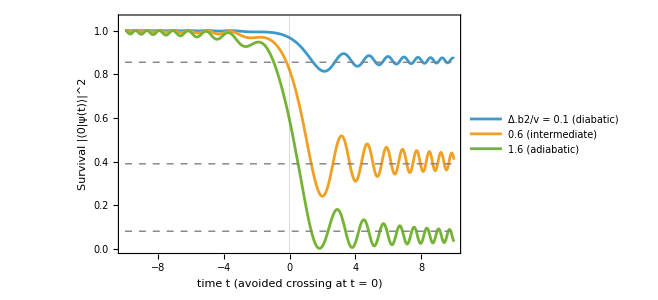

```mathematica
Plot[Evaluate@Table[survival[g, t], {g, ratios}], {t, -10, 10},
 Frame -> True, PlotRange -> {0, 1.05},
    FrameLabel -> {"time  t  (avoided crossing at t = 0)",
        "Survival  |⟨0|ψ(t)⟩|^2"},
    PlotLegends -> Placed[{"Δ.b2/v = 0.1  (diabatic)", "0.6  (intermediate)",
    "1.6  (adiabatic)"}, {0.78, 0.6}],
    Epilog -> {Gray, Dashed, Sequence @@ (Line[{{-10, Exp[-Pi #/2]}, {10, Exp[-Pi #/2]}}] & /@ ratios)},
    GridLines -> {{0}, None}]
```

The dashed lines are the textbook asymptotic value; the solid curves are the exact survival from the special-function propagator. Each drops through the crossing at t=0 and then oscillates about its asymptote with a slowly decaying envelope, the Landau-Zener-Stückelberg oscillations carried by the parabolic cylinder functions, which the asymptotic formula does not show. The asymptotic result is the long-time average of the exact answer, and the single ratio Δ^2/v orders the whole family: a fast (diabatic) sweep barely dips and stays in its branch, a slow (adiabatic) sweep transfers almost completely. The closed form gives the entire time-resolved crossing, oscillations included, where the asymptotic formula gives only the final number.

### A parametric circuit: QAOA, built entirely from a graph

QAOA is the canonical parametric circuit for optimization: one layer alternates a cost unitary e^(-iγ H_C) with a mixer e^-iθB, and the two angles are tuned to maximize a classical objective. The objective here is MaxCut: color the vertices of a graph with two colors s_i=±1 so that as many edges as possible join different colors, max_(s ∈ {±1}^n) ∑_((i,j)∈E) (1-s_i s_j)/2. Everything below is derived from the problem graph, so nothing is hardcoded. Take the complete graph on four vertices, K_4, a frustrated instance in which not all six edges can be cut:

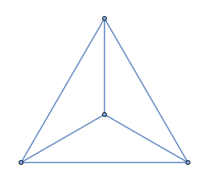

```mathematica
graph = CompleteGraph[4]
```

Read off the classical optimum, its best two-coloring of the vertices:

```mathematica
FindMaximumCut[graph]
```

{4,{{2,4},{1,3}}}

The classical answer is a cut of 4 of the 6 edges, splitting the four vertices into two pairs. Record the vertex count for reuse:

```mathematica
n = VertexCount[graph]
```

4

The MaxCut cost Hamiltonian H_C=∑_(i,j) (1-Z_i Z_j)/2 is assembled straight from the edge list, one (1-Z_i Z_j)/2 term per edge, and carries a label that will name its block in the diagram below:

```mathematica
hcost = QuantumOperator[Total[With[{id = QuantumOperator[StringJoin[ConstantArray["I", n]]]/2},
   (id - QuantumOperator["ZZ"/2, #] &) /@ (List @@@ EdgeList[graph])]], "Label" -> "Hamiltonian"]
```

QuantumOperator[…]

Change graph and this operator adapts to any graph.

The ansatz is built one labeled piece at a time. State prep puts every qubit in +, an equal superposition over all cuts:

```mathematica
stateprep = QuantumCircuitOperator[{StringJoin[ConstantArray["0", n]], "H" -> Range[n]}, "Label" -> "Prep"]
```

QuantumCircuitOperator[…]

The cost layer applies one ZZ(γ) rotation per edge, carrying the angle γ:

```mathematica
qcost = QuantumCircuitOperator[("R"[γ, "ZZ"] -> # &) /@ (List @@@ EdgeList[graph]), "Parameters" -> {γ}, "Label" -> "Cost"]
```

QuantumCircuitOperator[…]

The mixer applies an R_X(θ) to every vertex:

```mathematica
mixer = QuantumCircuitOperator[{"RX"[θ] -> VertexList[graph]}, "Parameters" -> {θ}, "Label" -> "Mixer"]
```

QuantumCircuitOperator[…]

Compose the three into one parametric layer:

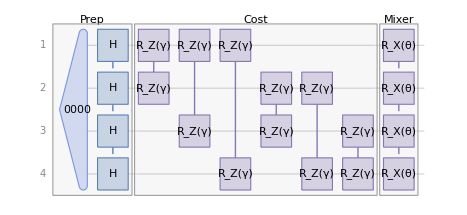

```mathematica
oneLayer = QuantumCircuitOperator[{stateprep, qcost, mixer}, "Parameters" -> {θ, γ}]
```

No qubit index was written by hand.

The cost landscape is the expectation ψ H_C ψ, and here QF uses a feature worth stating explicitly: a QuantumCircuitOperator can hold states as elements. Composing the prep circuit (the ket), the operator H_C, and the prep circuit's ["Dagger"] (the bra) builds ψ H_C ψ as a single object:

```mathematica
meanvalue = (oneLayer /* hcost /* oneLayer["Dagger"])
```

QuantumCircuitOperator[…]

That object draws itself:

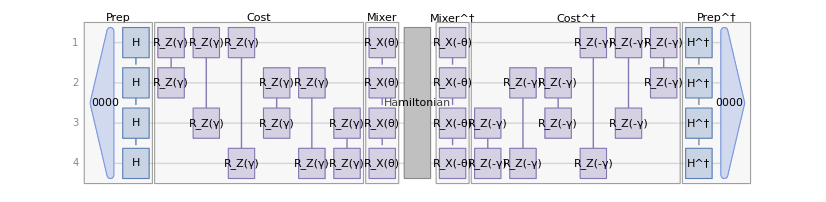

```mathematica
meanvalue["Diagram"]
```

The diagram shows the bra-ket structure block by block: the labeled Prep/Cost/Mixer layer, the Hamiltonian in the middle, and the daggered layer mirrored on the right. Calling the same object with []["Scalar"] returns the number, with no manual inner product:

```mathematica
landscape = FullSimplify[meanvalue[]["Scalar"], Element[{γ, θ}, Reals]]
```

3/8 (7+Cos[2 θ]+2 Cos[4 γ] Sin[θ]^2-8 Cos[γ]^2 Sin[γ] Sin[2 θ])

The exact QAOA energy landscape returns as ⟨H_C⟩(γ,θ)=3/8(7+cos 2θ+2cos 4γ sin^2 θ-8 cos^2 γ sin γ sin 2θ), a closed form in the two angles.

Because the landscape is a formula, the whole optimization problem can be looked at before it is solved. Plot the surface over a full period of both angles:

```mathematica
Plot3D[landscape, {γ, 0, 2 π}, {θ, 0, 2 π},
  PlotRange -> All,
  AxesLabel -> {"γ", "θ", "cost"},
  ColorFunction -> "TemperatureMap",
  PlotPoints -> 50]
```

-Graphics3D-

The surface is the entire variational problem: smooth, with period π in θ but 2π in γ (the cost angle enters through sin γ, not only 4γ, so γ needs a full 2π to repeat), and flat at the value 3 along the line γ=0, where the cost layer is inactive and the equal superposition cuts 3 of the 6 edges on average. What an experiment estimates point by point, with shot noise on every sample, is here a single exact surface, and its peaks are not read from a grid but certified algebraically. Take the maximum exactly:

```mathematica
Maximize[landscape, {θ, γ}]
```

{(3 (7-))/8,{θ→-2 (18 π-ArcTan[]),γ→-2 (5 π-ArcTan[])}}

The maximum returns as a closed-form algebraic number, a root of a cubic equal to ⟨H_C⟩_max, with the optimal angles likewise exact Root expressions. A single QAOA layer does not reach the true cut of 4, and the exact landscape certifies that ceiling as a cubic root rather than an estimate. Falling short is the generic behavior of one layer; a case where p=1 happens to saturate the cut is exceptional, and reaching 4 requires deeper QAOA with more layers. The point stands: the variational optimum is an exact symbolic quantity, a root of a cubic with closed-form angles, not a number sampled near the answer.

### A full many-body computation in closed form

The same construction extends to a genuine many-body computation. Build the 2-qubit Heisenberg Hamiltonian H=J (XX+YY+ZZ) symbolically (Hamiltonian simulation, a central application of a quantum computer):

```mathematica
hheis = J (QuantumOperator["XX"] + QuantumOperator["YY"] + QuantumOperator["ZZ"])
```

QuantumOperator[…]

Quench the product state 01 under it, that is, compute ψ(t)=e^-iHt 01:

```mathematica
psit = QuantumEvolve[hheis, QuantumState["01"], t]
```

QuantumState[…]

Display the evolved state at time t:

```mathematica
FullSimplify[psit] // TraditionalForm
```

ⅇ^(ⅈ J t) cos(2 J t)01-ⅈ ⅇ^(ⅈ J t) sin(2 J t)10

The evolved ket displays in closed form: the excitation oscillates coherently between 01 and 10 at angular frequency 2J, within an overall phase e^iJt. Now read off the entanglement entropy of one qubit as a function of time, S(t)=-Tr[ρ_1 log_2 ρ_1] with ρ_1=Tr_2 ψ(t)ψ(t), the standard measure of how entangled the two spins have become and a derived, nonlinear quantity:

```mathematica
s = FullSimplify[QuantumPartialTrace[psit, {2}]["VonNeumannEntropy"], t >0&&J ∈ Reals]
```

(Log[4 Csc[4 J t]^2]+Cos[4 J t] Log[Tan[2 J t]^2])/Log[4] b

QF returns the entire curve as a formula in t and J: the binary entropy of the two oscillating populations, zero whenever the state is a product, a full bit at the Bell points, periodic with the exchange oscillation. Because it is a formula, it can be differentiated, expanded, or solved in closed form, and the same approach extends to larger symbolic spin chains.

Plot it (at J=1):

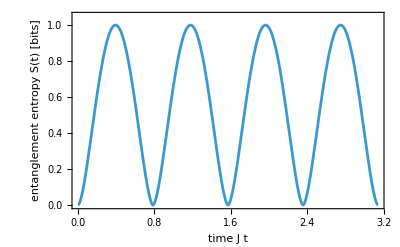

```mathematica
Plot[s /. {J -> 1}, {t, 0, Pi},
  Frame -> True, FrameLabel -> {"time  J t", "entanglement entropy  S(t)  [bits]"}, PlotRange -> {0, 1.05}]
```

## Claim 2: One object model spans all of quantum theory

Key feature: Claim 1 developed the symbolic dynamics of one object in depth; this claim shows the breadth of the object model. QF provides whole categories of object beyond unitary gates: open systems, generalized measurements, continuous-variable optics, phase space, and state estimation. Two properties hold throughout the model: every object carries its basis, and every object is defined in any finite dimension, qutrits and N-level systems as readily as qubits. The subject here is scope, the range of quantum theory that QF represents as objects one computes with directly.

### An open-system object: a quantum channel

A noise process is its own object, a QuantumChannel, not a gate. Take a generic pure qubit on the Bloch sphere, polar angle θ and azimuth ϕ, and confirm it is pure through the purity Tr[ρ^2], which equals 1 exactly for a pure state and drops below 1 for a mixed one. Build the state:

```mathematica
psi = QuantumState[{Cos[θ/2], Exp[I ϕ] Sin[θ/2]}]
```

QuantumState[…]

```mathematica
QuantumChannel["AmplitudeDamping"[γ]][psi]
```

QuantumState[…]

Read its purity:

```mathematica
psi["Purity"] // FullSimplify
```

1

The purity is 1, as it must be for any pure state.

Send it through amplitude damping, the decay channel ρ↦K_0 ρ K_0^†+K_1 ρ K_1^† with K_1=√γ 01 and K_0=00+√(1-γ)11: the excitation is lost with probability γ, the model of spontaneous emission. The question: how much purity does that cost, Tr[ρ^2]-Tr[ℰ_γ(ρ)^2], as an exact function of the damping rate γ and the state:

```mathematica
FullSimplify[psi["Purity"] - QuantumChannel["AmplitudeDamping"[γ]][psi]["Purity"],
  {θ ∈ Reals, ϕ ∈ Reals, 0 <= γ <= 1}]
```

-2 (-1+γ) γ Sin[θ/2]^4

The purity loss returns exactly as 2 γ(1-γ) sin^4 θ/2. The pure input has become mixed: irreversible, non-unitary dynamics captured directly as a channel object. The loss depends only on γ and the excited-state weight sin^2 (θ/2), never on the azimuth ϕ, and it vanishes at γ=0 (no damping), at γ=1 (fully relaxed to the pure ground state), and at θ=0 (0, which damping leaves untouched).

### The master equation, solved once for every state and every rate

A channel is a single instance of decoherence; the full dynamics is the Lindblad master equation, ρ̇=-i[H,ρ]+∑_i γ_i(L_i ρ L_i^†-1/2{L_i^†L_i,ρ}), and QuantumEvolve solves it symbolically. Given a density matrix whose four entries are symbols and rates that remain symbols, a single solution covers every qubit experiment at once. Set the physical region: positive rates, a real level splitting, and forward time:

```mathematica
$Assumptions = γ1 > 0 && γϕ >= 0 && Ω ∈ Reals && t >= 0;
```

Write the decay operator σ_-=01 as its matrix, so it empties the excited state:

```mathematica
σm = QuantumOperator[{{0, 1}, {0, 0}}]
```

QuantumOperator[…]

Take the all-states-at-once initial density matrix ρ_0, every entry a symbol:

```mathematica
ρ0 = QuantumState[Array[ρ, {2, 2}]]
```

ρ(1,1)00+ρ(1,2)01+ρ(2,1)10+ρ(2,2)11

Solve the master equation for a qubit with level splitting Ω, energy relaxation at γ_1 (jump operator √γ_1 σ_-), and pure dephasing at γ_ϕ (jump operator √γ_ϕ Z):

```mathematica
ρt = QuantumEvolve[Ω/2 QuantumOperator["Z"],
   {Sqrt[γ1] σm, Sqrt[γϕ] QuantumOperator["Z"]}, ρ0, t]
```

QuantumState[…]

Read its density matrix in the computational basis:

```mathematica
FullSimplify /@ Normal[ρt["Computational"]["DensityMatrix"]] // MatrixForm
```

(ρ[1,1]+(1-ⅇ^(-t γ1)) ρ[2,2] | ⅇ^(-1/2 t (γ1+4 γϕ+2 ⅈ Ω)) ρ[1,2]
ⅇ^(-1/2 t (γ1+4 γϕ-2 ⅈ Ω)) ρ[2,1] | ⅇ^(-t γ1) ρ[2,2])

The matrix returns exactly as the complete relaxation law for an arbitrary qubit:

ρ(t)=(ρ_11+(1-e^(-γ_1 t))ρ_22 | ρ_12 e^(-(γ_1/2+2 γ_ϕ+iΩ)t)
ρ_21 e^(-(γ_1/2+2 γ_ϕ-iΩ)t) | ρ_22 e^(-γ_1 t))

The excited population decays at γ_1, the lost population moves to the ground state, and the coherence precesses at Ω while decaying at Γ_2=γ_1/2+2 γ_ϕ: every experiment on every qubit, in one matrix. With T_1=1/γ_1 and T_2=1/Γ_2 read from the exponents, the textbook bound between the two times is a theorem about this solution:

```mathematica
Reduce[ForAll[{γ1, γϕ}, γ1 > 0 && γϕ >= 0, 1/(γ1/2 + 2 γϕ) <= 2/γ1]]
```

True

The reduction returns True: T_2≤2 T_1 holds for every admissible rate pair, obtained from the computation rather than quoted from a textbook, and reducing the corresponding equality for the dephasing rate, Reduce[1/(γ1/2 + 2 γϕ) == 2/γ1, γϕ], returns γ_ϕ=0 (for γ_1≠0): the factor of two is saturated exactly when dephasing vanishes.

### A generalized measurement: a POVM

Real detectors are not always projective. A POVM is a set of positive effects {E_i} summing to the identity, ∑_i E_i=I, with outcome probabilities given by the Born rule p_i=Tr[ρ E_i]; one is built from a list of effects with QuantumMeasurementOperator[{E1, E2, ...}]. A symmetric informationally complete POVM is the maximally symmetric case: d^2 rank-one effects E_i=1/d ψ_iψ_i with equal pairwise overlaps ψ_iψ_j^2=1/(d+1), four outcomes on a two-level system, pointing along the vertices of a tetrahedron in the Bloch ball. Measure a generic Bloch qubit ψ(θ,ϕ), applying the Born rule symbolically to all four effects. Build the state:

```mathematica
psi = QuantumState[{Cos[θ/2],Sin[θ/2]Exp[ⅈ ϕ]}]
```

QuantumState[…]

Build the tetrahedron SIC POVM:

```mathematica
sic = QuantumMeasurementOperator["TetrahedronSICPOVM"]
```

QuantumMeasurementOperator[…]

Apply the Born rule p_i=Tr[ρ E_i] to all four effects at once:

```mathematica
probs = FullSimplify[ComplexExpand[Tr[psi["DensityMatrix"] . Normal[#]] & /@ sic["POVMElements"]]]//Chop
```

{1/4 (1+Cos[θ]),1/12 (3-Cos[θ]-√2 Sin[θ] (Cos[ϕ]+√3 Sin[ϕ])),1/12 (3-Cos[θ]-√2 Cos[ϕ] Sin[θ]+√6 Sin[θ] Sin[ϕ]),1/12 (3-Cos[θ]+2 √2 Cos[ϕ] Sin[θ])}

The four probabilities return exactly as p_i=1/4(1+r̂·(n̂)_i), the first reading (1+cos θ)/4 and the others 1/12(3-cos θ+√2 sin θ (…)) along the remaining tetrahedron directions (n̂)_i, with r̂ the state's Bloch vector; they sum to 1 identically (verified). Pin the state to the north pole and the general formulas collapse to numbers:

```mathematica
probs /. θ -> 0
```

{1/2,1/6,1/6,1/6}

The distribution collapses to simple rationals: 0 assigns probability one half to the tetrahedron vertex nearest the pole and one sixth to each of the other three. Because the SIC is informationally complete, these four probabilities are not merely statistics of the state; they determine the state: θ and ϕ can be recovered from them, which is what makes SIC measurements a natural basis for tomography.

The SIC is not only a symbolic Born-rule calculation; it is a measurement that drops directly into a circuit, alongside the gates, on any chosen wire. Place the tetrahedron SIC as a measurement on the first qubit:

```mathematica
sicQubit1 = QuantumMeasurementOperator["TetrahedronSICPOVM", {1}]
```

QuantumMeasurementOperator[…]

Build a small entangling circuit that ends in that POVM:

```mathematica
circ = QuantumCircuitOperator[{"H" , "RY"[1.05] -> 2,
       "CNOT" , "RZ"[2.04], sicQubit1}]
```

QuantumCircuitOperator[…]

Draw it:

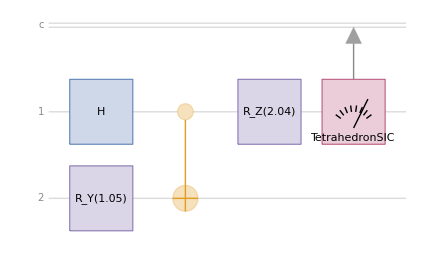

```mathematica
circ["Diagram"]
```

The diagram shows the four-outcome POVM sitting at the end of the first wire like any other measurement. Applying the circuit returns a QuantumMeasurement, and that object draws its own outcome statistics:

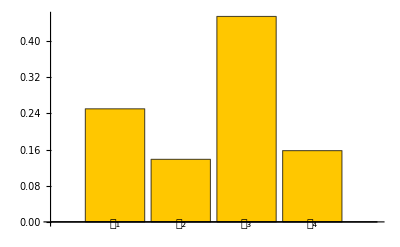

```mathematica
circ[]["ProbabilitiesPlot"]
```

Four bars summing to one, one tetrahedron outcome suppressed and another enhanced: the SIC measurement of qubit 1. Here qubit 1 is entangled with qubit 2, so its reduced state is mixed, its Bloch vector lies inside the ball (length less than 1), and the four probabilities are correspondingly drawn in from the pure-state extremes toward the uniform value 1/4. The same informationally complete measurement reports a mixed, entangled qubit as faithfully as a pure one, which is what tomography of a real, noisy qubit requires.

### Continuous-variable quantum optics

Bosonic Fock space, not qubits. The state of an ideal laser mode is the coherent state α=e^(-α^2/2)∑_(n=0)^∞ α^n/(√(n!))n, defined as the eigenstate of the photon annihilation operator, â α=αα, with a complex eigenvalue α because â is not Hermitian. QF builds these objects directly in a truncated Fock space (sixteen levels by default). Check the eigenvalue equation with α fully symbolic. Build the annihilation operator:

```mathematica
aOp = AnnihilationOperator[]
```

QuantumOperator[…]

Build the coherent state, left unnormalized so the symbolic algebra stays clean:

```mathematica
alphaKet = CoherentState["Normalized" -> False]
```

QuantumState[…]

Subtract αα from â α and read the amplitudes (the truncation edge excluded):

```mathematica
Simplify[Most[(aOp[alphaKet] - α alphaKet)["AmplitudesList"]]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Every amplitude of â α-αα returns identically zero in the symbolic α (the truncation-edge amplitude excluded): the defining equation, verified for the whole family of coherent states at once.

The property that earns these states the name "most classical states of light" is dynamical: under the oscillator Hamiltonian H=ω ((â)^†â+1/2) a coherent state remains a coherent state, e^-iHt α=e^(-iωt/2)α e^-iωt, its label α rotating about the origin of phase space at frequency ω, like a classical oscillator amplitude, up to the overall phase e^(-iωt/2). Compute the oscillator propagator with QuantumEvolve, symbolically:

```mathematica
uosc = QuantumEvolve[ω (aOp["Dagger"] @ aOp + 1/2), None, t]
```

QuantumOperator[…]

Then check the coherent-state identity it implies, with α, ω, and t all symbols:

```mathematica
uosc @ CoherentState[] == E^(-I ω t/2) CoherentState[][α E^(-I ω t)]
```

True

True, with α, ω, and t all symbols: one evolution determines the dynamics of every coherent state at every frequency, an exact statement about the family rather than a simulation of one member. (QF's state == compares up to global phase, so this fixes the label α→α e^-iωt; the vacuum phase e^(-iωt/2) is exact but lies in the global phase that == ignores, and appears only in an amplitude-level comparison.)

What distinguishes this most-classical light from other states is photon statistics. The second-order coherence at zero delay, g^(2)(0)=⟨a^†a^†a a⟩/(⟨a^†a⟩^2)=⟨n(n-1)⟩/⟨n⟩^2, is the normalized probability of detecting two photons at once; it classifies light by photon statistics: antibunched (<1, nonclassical), coherent (=1), and bunched thermal (>1).

```mathematica
g2s = <|"Fock" -> G2Coherence[FockState[1]], "Coherent" -> G2Coherence[CoherentState[20][1.5+ⅈ 2]],
  "Thermal" -> G2Coherence[ThermalState[1.0, 20]]|>
```

<|Fock→0,Coherent→0.999957-7.32665×10^-18 ⅈ,Thermal→1.99968|>

Each class takes the value the formula predicts: zero for the single photon, one for the laser, two for thermal light. The three values chart directly:

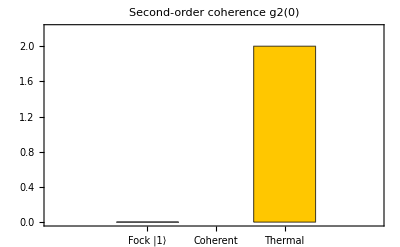

```mathematica
BarChart[g2s, ChartLabels -> {"Fock |1⟩", "Coherent", "Thermal"},
  PlotLabel -> "Second-order coherence g2(0)", Frame -> True, PlotRange -> {0, 2.2}]
```

The ordering on the chart, antibunched below 1, coherent at 1, bunched above, is the photon-statistics signature that distinguishes these light sources where a single intensity measurement cannot.

### Phase-space quasi-probabilities: Wigner and Husimi

The Wigner function is the phase-space quasi-probability W(x,p)=1/π∫x-yρx+y e^(2ipy)dy. It integrates to 1 like a probability density but, unlike one, can take negative values, and that negativity is a signature of nonclassicality with no classical analogue. A clear example is the Schrodinger cat state, the even superposition (α+-α)/𝒩 of two coherent states of opposite phase, here with α=2. Build its Wigner function on a phase-space window:

```mathematica
wigner = WignerRepresentation[CatState[][2, 0], {-6, 6}, {-2, 2}, "GridSize" -> 90]
```

InterpolatingFunction[…]

Read it at two representative points, the origin and half a fringe away in momentum:

```mathematica
{wigner[0, 0], wigner[0, 1/2]}
```

{0.318237,-0.235638}

The first value is positive, the second negative. The first is the important one: at the midpoint between the two coherent components, where a classical mixture of them would place almost no weight, the Wigner function instead has its strongest feature, an interference peak that reaches the ceiling 1/π that no Wigner function can exceed. The even cat is a parity eigenstate, so W(0,0)=1/π exactly (here up to the Fock truncation), not merely close to it; the neighboring fringe is firmly negative.

The Wigner function is one of a family of phase-space quasi-probabilities, and its smoothed counterpart removes the negativity. The Husimi-Q function Q(x,p)=1/π αρα, with α=(x+ip)/√2, is the Wigner function convolved with a coherent-state Gaussian; that smoothing makes it non-negative everywhere, at the cost of removing the nonclassicality the Wigner reveals. Build it over the same window, slightly taller in p since the Husimi is wider:

```mathematica
husimi = HusimiQRepresentation[CatState[][2, 0], {-6, 6}, {-3, 3}, "GridSize" -> 90]
```

InterpolatingFunction[…]

Read it at the origin where the Wigner peaked:

```mathematica
husimi[0, 0]
```

0.00582748

The Husimi is close to zero there, in contrast to the Wigner's sharp peak: the Gaussian average has cancelled the oscillating fringes. Plot the two surfaces side by side:

```mathematica
Row[{
   Plot3D[wigner[x, p], {x, -6, 6}, {p, -2, 2}, PlotRange -> All, Mesh -> None,
     PlotPoints -> 50, ColorFunction -> "SunsetColors",
     AxesLabel -> {"x", "p", "W"}, PlotLabel -> "Wigner W(x,p)", ImageSize -> Small],
   Plot3D[husimi[x, p], {x, -6, 6}, {p, -3, 3}, PlotRange -> All, Mesh -> None,
     PlotPoints -> 50, ColorFunction -> "SunsetColors",
     AxesLabel -> {"x", "p", "Q"}, PlotLabel -> "Husimi Q(x,p)", ImageSize -> Small]}]
```

-Graphics3D--Graphics3D-

The same cat state, two quasi-probabilities. The Wigner on the left has the two Gaussian lobes at x=±2 √2, the coherent components, together with the interference ridge oscillating above and below zero between them; that negativity is the signature of the superposition. The Husimi on the right keeps only the two smooth, non-negative lobes, each near 1/2π, with the fringes smoothed flat. Both are properly normalized quasi-probabilities, the Wigner integrating to 1 over dx dp and the Husimi to 1 over d^2 α=dx dp/2 (equivalently, to 2 over dx dp), but only the Wigner can take negative values, which is why Wigner negativity, and not the always-positive Husimi, is the witness of nonclassicality. Decoherence erases the Wigner fringes and leaves the lobes, moving the left picture toward the right.

### Every object carries its basis

The scope extends inward as well: every state, operator, and measurement above is stored together with the basis it is written in. A basis is a stored matrix B whose rows are the basis vectors in computational coordinates, a change of basis is the similarity transformation A_ℬ=B^-1 AB, and objects written in different bases reconcile automatically through the computational frame. About three dozen named bases are provided (Bell, Fourier, Schwinger, Dirac, Gell-Mann, Wigner, MUB, SIC), and the same mechanism converts non-computational measurements for OpenQASM export and supplies the Bell-derived basis used in two-qubit KAK gate compilation. The representation changes while the physics does not: take the qubit +, the superposition (0+1)/√2 in the computational basis, and write it in the X basis instead:

```mathematica
QuantumOperator["XY"]["Diagram"]
```

-Graphics-

```mathematica
QuantumState["+"]["Diagram"]
```

-Graphics-

```mathematica
QuantumState["+"]
```

1/(√2)0+1/(√2)1

```mathematica
QuantumState[QuantumState["+"], QuantumBasis[<|"my-0"->{1,2},"my-1"->{1+ⅈ,3}|>]] // TraditionalForm
```

(4/5+(3 ⅈ)/5)/(√2)my-0+((1/5+(2 ⅈ)/5)/(√2)-(1/5+(2 ⅈ)/5) √2)my-1

The state renders as the single ket x_+: in its own eigenbasis + is one basis vector, not a superposition. Same state, different coordinates.

The measurable content is untouched by any such rewriting, and nothing here is qubit-bound. Take a spin-1 particle in its m_x=+1 eigenstate, defined directly in the J_x basis:

```mathematica
mx = QuantumState[{0, 0, 1}, "JX"[1]]
```

QuantumState[…]

Display it:

```mathematica
mx // TraditionalForm
```

J_1^x

The state renders as the single ket J_1^x. Re-express it in the computational (J_z) basis:

```mathematica
mxZ = QuantumState[mx, "Computational"[3]]
```

QuantumState[…]

Display it again:

```mathematica
mxZ // TraditionalForm
```

1/2 0+1/(√2)1+1/2 2

The same state spreads into a three-term superposition over the J_z levels: one ket in its own basis, a sum in the other. The named operator J_x is itself stored in its own eigenbasis, so the expectation ⟨J_x⟩=ψ J_x ψ involves three declared bases at once; compute it from both representations of the state:

```mathematica
<|"JX basis" -> mx["Dagger"][QuantumOperator["JX"[1]][mx]]["Scalar"],
  "Computational basis" -> mxZ["Dagger"][QuantumOperator["JX"[1]][mxZ]]["Scalar"]|>
```

<|JX basis→1,Computational basis→1|>

Both entries return as ⟨J_x⟩=1: the state in either coordinate system, the operator in a third, and QF reconciled them all; the invariant survives every change of coordinates.

### Any finite dimension: a spin-1 qutrit and a five-site ring

The same spin-1 system supports genuine three-level dynamics, not just a change of basis, and the representation extends to any dimension. Its zero-field-splitting Hamiltonian H=2d J_z^2+e (J_x^2-J_y^2), the model of an NV-center defect, is built from QF's native spin-1 operators with both couplings left symbolic. First the three spin-1 operators:

```mathematica
{jx, jy, jz} = QuantumOperator /@ {"JX"[1], "JY"[1], "JZ"[1]}
```

{QuantumOperator[…],QuantumOperator[…],QuantumOperator[…]}

Assemble the zero-field-splitting Hamiltonian from them:

```mathematica
hzfs = 2 d jz^2 + e (jx^2 - jy^2)
```

QuantumOperator[…]

Display its matrix:

```mathematica
hzfs["Matrix"] // MatrixForm
```

(d+e/2 | 0 | d+e/2
0 | 2 d-e | 0
d+e/2 | 0 | d+e/2)

```mathematica
EigenvalueDecomposition[({{d+e/2, 0, d+e/2}, {0, 2 d-e, 0}, {d+e/2, 0, d+e/2}})]
```

{{{-1,0,1},{0,1,0},{1,0,1}},{{0,0,0},{0,2 d-e,0},{0,0,2 d+e}}}

```mathematica
EigenvalueDecomposition[({{d+e/2, 0, d+e/2}, {0, 2 d-e, 0}, {d+e/2, 0, d+e/2}})][[2]]//MatrixForm
```

(0 | 0 | 0
0 | 2 d-e | 0
0 | 0 | 2 d+e)

```mathematica
hzfs["Eigenvectors"]
```

{{0,1,0},{1/(√2),0,-1/(√2)},{1/(√2),0,1/(√2)}}

The operator is fully symbolic, and its matrix is displayed in the basis the algebra carried with it, the J_x eigenbasis: the couplings remain symbols, and the coordinates remain attached to the object.

A Hamiltonian is simplest in its energy eigenbasis, and the operator provides its own eigenvectors. Build a basis from them and read H there:

```mathematica
QuantumOperator[hzfs, QuantumBasis[hzfs["Eigenvectors"]]]["Matrix"] // Normal // FullSimplify//MatrixForm
```

(0 | 0 | 0
0 | 2 d-e | 0
0 | 0 | 2 d+e)

The matrix returns exactly as diag(0, 2d-e, 2d+e): the zero-field-split spectrum in closed form, symbols intact. Building a basis from an object's own eigenvectors works in any dimension, and the spin-j operators are provided natively for every j.

Dimension need not be a power of two either. A particle hopping on an N-site ring lives in an N-dimensional Hilbert space, here N=5, with the tight-binding Hamiltonian H=-∑_(j=1)^N (jj+1+j+1j), site N+1 identified with site 1. Fix the ring size:

```mathematica
n = 5;
```

Build the hopping matrix, -1 for every pair of neighboring sites:

```mathematica
ring = -Table[
    Boole[Mod[i - j, n] == 1 || Mod[j - i, n] == 1], {i, n}, {j, n}];
```

Look at it in the site basis:

```mathematica
ring // MatrixForm
```

(0 | -1 | 0 | 0 | -1
-1 | 0 | -1 | 0 | 0
0 | -1 | 0 | -1 | 0
0 | 0 | -1 | 0 | -1
-1 | 0 | 0 | -1 | 0)

The matrix displays as a circulant: -1 on the two neighbor diagonals and in the far corners, the bond that closes the chain into a ring, and zero everywhere else. In the site basis the physics is local hopping; by Bloch's theorem the same operator should be diagonal in the momentum (Fourier) basis. Rewrite it there and read the diagonal:

```mathematica
QuantumBasis["Fourier"[n]]["Association"]
```

<|F_1→{1/(√5),1/(√5),1/(√5),1/(√5),1/(√5)},F_2→{1/(√5),ⅇ^((2 ⅈ π)/5)/(√5),ⅇ^((4 ⅈ π)/5)/(√5),ⅇ^(-(4 ⅈ π)/5)/(√5),ⅇ^(-(2 ⅈ π)/5)/(√5)},F_3→{1/(√5),ⅇ^((4 ⅈ π)/5)/(√5),ⅇ^(-(2 ⅈ π)/5)/(√5),ⅇ^((2 ⅈ π)/5)/(√5),ⅇ^(-(4 ⅈ π)/5)/(√5)},F_4→{1/(√5),ⅇ^(-(4 ⅈ π)/5)/(√5),ⅇ^((2 ⅈ π)/5)/(√5),ⅇ^(-(2 ⅈ π)/5)/(√5),ⅇ^((4 ⅈ π)/5)/(√5)},F_5→{1/(√5),ⅇ^(-(2 ⅈ π)/5)/(√5),ⅇ^(-(4 ⅈ π)/5)/(√5),ⅇ^((4 ⅈ π)/5)/(√5),ⅇ^((2 ⅈ π)/5)/(√5)}|>

```mathematica
QuantumBasis["X"[2]]["Association"]
```

<|𝓍_+→{1/(√2),1/(√2)},𝓍_−→{1/(√2),-1/(√2)}|>

```mathematica
QuantumBasis["X"[n]]["Association"]
```

<|𝓍_0→{1/(√5),1/(√5),1/(√5),1/(√5),1/(√5)},𝓍_1→{1/(√5),-(-1)^(3/5)/(√5),-(-1)^(1/5)/(√5),(-1)^(4/5)/(√5),(-1)^(2/5)/(√5)},𝓍_2→{1/(√5),-(-1)^(1/5)/(√5),(-1)^(2/5)/(√5),-(-1)^(3/5)/(√5),(-1)^(4/5)/(√5)},𝓍_3→{1/(√5),(-1)^(4/5)/(√5),-(-1)^(3/5)/(√5),(-1)^(2/5)/(√5),-(-1)^(1/5)/(√5)},𝓍_4→{1/(√5),(-1)^(2/5)/(√5),(-1)^(4/5)/(√5),-(-1)^(1/5)/(√5),-(-1)^(3/5)/(√5)}|>

```mathematica
QuantumOperator[QuantumOperator[ring], QuantumBasis["X"[n]]]
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating Abs[-(2 (-1/5 (-1)^(1/5)-1/5 (-1)^(2/5)+1/5 (-1)^(3/5)+1/5 (-1)^(4/5)))/(√5 (-Power[«2»] Power[«2»]-Power[«2»] Power[«2»]+Power[«2»] «1»+Power[«2»] Power[«2»]))+(2 («1»)^(«1») («1»))/(√5 («1»))-(«1»)/(«1»)+(«1»)/(«1»)-(2 (-1)^(4/5) («1»))/(√5 («1»))].

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating √(((Times[«2»]+Times[«2»])/(√5 Plus[«2»])+(Times[«1»]+«1»)/(√5 Plus[«1»])+«1»+(«1»)/(«1»)+(Times[«2»]+Times[«2»])/(√5))^2+((2 («1»))/(√5 Plus[«2»])+(2 «1»)/(√5)+(2 («1»))/(√5))^2).

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating Abs[-(2 (-1/5 (-1)^(1/5)-1/5 (-1)^(2/5)+1/5 (-1)^(3/5)+1/5 (-1)^(4/5)))/(√5 (-Power[«2»] Power[«2»]-Power[«2»] Power[«2»]+Power[«2»] «1»+Power[«2»] Power[«2»]))+(2 («1»)^(«1») («1»))/(√5 («1»))-(«1»)/(«1»)+(«1»)/(«1»)-(2 (-1)^(4/5) («1»))/(√5 («1»))].

General::stop: Further output of N::meprec will be suppressed during this calculation.

QuantumOperator[…]

```mathematica
Normal @ Chop @
  N @ Diagonal[
    QuantumOperator[QuantumOperator[ring], QuantumBasis["Fourier"[n]]][
     "Matrix"]]
```

{-2.,-0.618034,1.61803,1.61803,-0.618034}

The diagonal returns exactly the tight-binding dispersion E(k)=-2cos (2πk/N) at the five Bloch momenta, and the off-diagonal terms vanish: a five-level system, diagonalized by a named basis the same way a qubit would be.

### State estimation: tomography from measured counts

Tomography is the inverse of measurement: recover an unknown state from the statistics of measurements in several bases, and it is part of the same object model. The three qubit Pauli bases X,Y,Z are mutually unbiased and together informationally complete: their outcome frequencies estimate the three expectations that pin down the density matrix through ρ=1/2(I+⟨X⟩X+⟨Y⟩Y+⟨Z⟩Z). QF performs the entire procedure. First, pick an unknown state to reconstruct:

```mathematica
true = QuantumState[N @ {Cos[Pi/6], Sin[Pi/6] Exp[I Pi/4]}]
```

0.8660250+(0.353553+0.353553 ⅈ)1

Simulate 2000 measurement shots in each of the three Pauli bases (seeded for reproducibility):

```mathematica
SeedRandom[42];
data = QuantumMeasurementSimulation[true, QuantumMeasurementOperator /@ {"X", "Y", "Z"}, 2000]
```

<|QuantumMeasurementOperator[…]→{1605,395},QuantumMeasurementOperator[…]→{1620,380},QuantumMeasurementOperator[…]→{1504,496}|>

Look at the raw counts:

```mathematica
Values[data]
```

{{1605,395},{1620,380},{1504,496}}

Three pairs of counts return, one per basis: multinomially sampled tallies scattered around the Born-rule proportions, different on every fresh sample, and all a real experiment ever sees.

Now pass the counts to the estimator, which performs linear inversion followed by maximum-likelihood:

```mathematica
est = QuantumStateEstimate[data]
```

QuantumStateEstimation[…]

Read the reconstructed density matrix:

```mathematica
est["MaximumLikelihoodState"]["DensityMatrix"] // Normal // Chop
```

{{0.751442,0.301831-0.309314 ⅈ},{0.301831+0.309314 ⅈ,0.248558}}

The recovered matrix agrees closely with the true one, whose exact entries are ρ_11=3/4 and ρ_12=(√3)/4 e^(-iπ/4), with entry-wise residuals at the scale shot noise sets, ∼1/√2000; which entries deviate, and by how much, changes with every fresh sample. To summarize the reconstruction in one number, compute its fidelity F(ρ,σ)=Tr √(√ρ σ √ρ) to the original state, equal to 1 exactly when the two states coincide:

```mathematica
QuantumSimilarity[true, est["MaximumLikelihoodState"]]
```

0.999985

The fidelity is close to 1, its deviation set by the shot noise, of order 1/√2000: the unknown state recovered from finite, noisy synthetic data, using only counts in three bases. Beyond these unitary measurement bases, the same basis mechanism continues into the over-complete operator frames, where B^-1 becomes a dual frame and a state becomes a probability vector, the mechanism behind the SIC measurement above.

## Claim 3: Measurement records are quantum wires, and feedforward is a controlled gate

Key feature: Claim 2 used measurement to estimate a state; here measurement itself is decomposed. QF implements a projective measurement as von Neumann's measurement interaction, not as a collapse: it appends a pointer qudit and entangles it with the system, Vψ=∑_k (P_k ψ)⊗k. The record of the measurement is therefore itself a quantum wire, numbered 0,-1,-2,… alongside the system wires; every branch remains in the state, and feedforward, acting on the system conditioned on an earlier outcome, is simply a gate controlled on a record wire. Protocols that combine measurement with conditioned gates, teleportation, error correction, measurement-based computing, remain inside one symbolic object.

Closest competitor. Cirq and PennyLane both ship a defer_measurements transform that turns mid-circuit measurement into exactly this controlled-on-a-record mechanism; QF's edge is generality, not kind: arbitrary observables, degenerate rank-k projectors, POVM and Naimark dilations, qudits, and a record that can be read jointly and inverted, not just a deferred computational-basis bit.

### Teleportation: the classical channel as a quantum wire

Teleportation is the clearest illustration of a measurement record used as a wire. In the textbook protocol Alice measures her two qubits in the Bell basis and sends the two classical bits to Bob, who applies X^m_2 Z^m_1 to his half of an entangled pair. The deferred-measurement principle states that this classical communication is not required: the corrections can be conditioned on the records themselves. Build exactly that, qubit 1 carrying the unknown state, qubits 2 and 3 in a Bell pair:

```mathematica
tele = QuantumCircuitOperator[{
    "H" -> 2, "CNOT" -> {2, 3},
    "CNOT" -> {1, 2}, "H" -> 1,
    {1}, {2},
    "CNOT" -> {-1, 3},
    "CZ" -> {0, 3}}]
```

QuantumCircuitOperator[…]

Draw the protocol:

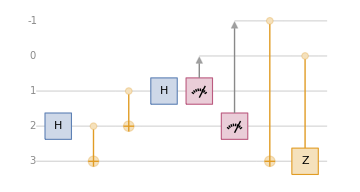

```mathematica
tele["Diagram"]
```

The diagram is the whole protocol. The two measurements, written as the bare qubit lists {1} and {2}, place their outcomes on the record wires described in the introduction, numbered 0 and -1 below the system wires. The corrections then act from those record wires: "CNOT" -> {-1, 3} is an X on Bob's qubit controlled by the second record, and "CZ" -> {0, 3} a Z controlled by the first, both ordinary controlled gates with a record wire in the control position. No classical bit ever leaves the object; the classical channel has become two record wires, promoted to a coherent quantum resource rather than removed (a record wire is a more expensive resource than a classical bit, not a free one).

Teleport a generic Bloch qubit ψ(θ,ϕ)=cos θ/2 0+e^iϕ sin θ/2 1. The protocol succeeds if Bob ends up holding exactly the input, ρ_Bob=ψψ, which for a qubit means the two Bloch vectors coincide. First build the input state:

```mathematica
psi = QuantumState[{Cos[θ/2], Exp[I ϕ] Sin[θ/2]}]
```

QuantumState[…]

Read its Bloch vector:

```mathematica
FullSimplify[psi["BlochVector"], {θ ∈ Reals, ϕ ∈ Reals}]
```

{Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]}

It returns the textbook (sin θcos ϕ, sin θsin ϕ, cos θ). Now run the protocol:

```mathematica
out = tele[QuantumTensorProduct[psi, QuantumState["00"]]]
```

QuantumState[…]

Read Bob's Bloch vector, the partial trace discarding Alice's two qubits and the two records, the four wires before Bob's:

```mathematica
FullSimplify[QuantumPartialTrace[out, {1, 2, 3, 4}]["BlochVector"], {θ ∈ Reals, ϕ ∈ Reals}]
```

{Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]}

Bob's Bloch vector returns as the same (sin θcos ϕ, sin θsin ϕ, cos θ), identically in θ and ϕ: every pure state teleports exactly, the recovered state equals the input, with the classical channel carried as record wires inside the object rather than eliminated.

### A coherent error, digitized and corrected

The three-qubit repetition code encodes α0+β1 as α000+β111 and protects it against bit flips. The subtlety is that real errors are not discrete flips; here the error is a coherent rotation R_X(2θ) on the middle qubit, between no error (θ=0) and a full flip (θ=π/2). The founding theorem of error correction states that measuring the syndrome digitizes this continuous error into those two discrete cases, shown here symbolically.

First the syndrome measurement. The parity Z_1 Z_2 must be measured without learning anything else about the state: a degenerate projective measurement with two rank-two projectors P_±=(I±Z⊗Z)/2, which is precisely what QuantumMeasurementOperator accepts as a list of projectors. First the single-qubit identity:

```mathematica
id2 = IdentityMatrix[2];
```

The two-qubit parity operator Z⊗Z:

```mathematica
zz = KroneckerProduct[PauliMatrix[3], PauliMatrix[3]];
```

The syndrome measurement on a pair of qubits, the two rank-two projectors P_±=(I±Z⊗Z)/2:

```mathematica
syn[q1_, q2_] := QuantumMeasurementOperator[
   {QuantumOperator[(KroneckerProduct[id2, id2] + zz)/2, {q1, q2}],
    QuantumOperator[(KroneckerProduct[id2, id2] - zz)/2, {q1, q2}]}, {q1, q2}];
```

Then the full code: encode, inflict the coherent error, measure both parities, and decode each of the four syndrome patterns into its correction. The decoder is three feedforward gates with mixed polarities, "C"["X", ones, zeros] conditions an X on some records reading 1 and others reading 0. First the encoder:

```mathematica
enc = QuantumCircuitOperator[{"CNOT" , "CNOT" -> {1, 3}},
   "Label" -> "Encode"]
```

QuantumCircuitOperator[…]

Then the full code, encoder through feedforward correction:

```mathematica
qec = QuantumCircuitOperator[{enc,
        "RX"[2 θ] -> 2,
        syn[1, 2], syn[2, 3],
        "C"["X", {0}, {-1}],
        "C"["X" -> 2, {0, -1}, {}],
        "C"["X" -> 3, {-1}, {0}]}]
```

QuantumCircuitOperator[…]

Draw it:

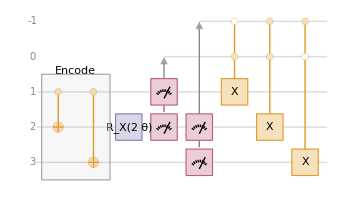

```mathematica
qec["Diagram"]
```

The diagram lays out the whole code on five wires: the labeled Encode block spreading the data qubit across the three code qubits, the R_X(2θ) error on qubit 2, the two parity measurements placing their syndromes on record wires 0 and -1, and the three corrections acting from those records, each an X controlled on one record and anti-controlled on the other. Run it on a fully symbolic data qubit:

```mathematica
coded = qec[QuantumTensorProduct[QuantumState[{α, β}], QuantumState["00"]]]
```

QuantumState[…]

Read the joint distribution of the two syndrome records, the diagonal of their reduced density matrix (the records sit on the first two of the five wires, the data on the last three):

```mathematica
Assuming[{θ ∈ Reals, α ∈ Reals, β ∈ Reals, α^2 + β^2 == 1},
  FullSimplify[ComplexExpand[Diagonal[Normal[QuantumPartialTrace[coded, {3, 4, 5}]["DensityMatrix"]]]]]]
```

{Cos[θ]^2,0,0,Sin[θ]^2}

The four syndrome weights return as {cos^2 θ, 0, 0, sin^2 θ}: the continuous rotation has been digitized. The code never sees a partial error; it sees "no error" with probability cos^2 θ or "qubit 2 flipped" with probability sin^2 θ, and the weights are independent of α and β, which is what "measuring the syndrome without learning the state" means.

The feedforward gates then act inside each branch. The claim to check: the corrected state matches the ideal codeword α000+β111 at fidelity F=1, for every input and every error angle. Compute F symbolically:

```mathematica
Assuming[{θ ∈ Reals, α ∈ Reals, β ∈ Reals, α^2 + β^2 == 1},
  FullSimplify[ComplexExpand[QuantumSimilarity[QuantumPartialTrace[coded, {1, 2}],
    enc[QuantumTensorProduct[QuantumState[{α, β}], QuantumState["00"]]], "Fidelity"]]]]
```

1

The fidelity returns as exactly 1, for every input (α,β) and every error angle θ: not a high number for one sampled case, but the digitization-of-errors theorem itself, obtained from the computation. (The cell fixes real amplitudes so the symbolic fidelity closes cleanly; the result is in fact independent of α,β and remains 1 for complex amplitudes as well.)

### Run the measurement backwards

Because no branch was discarded, the measurement is a reversible interaction, and reversible in the laboratory, not only on paper. That a partial measurement can be undone while its record stays coherent, before it irreversibly decoheres, is an experimental fact: the probabilistic reversal, or 'uncollapsing', of a weak measurement has been demonstrated on a superconducting phase qubit (Katz et al., Phys. Rev. Lett., 2008), returning the qubit to its pre-measurement state on a heralded subset of runs. The cell below is the deterministic idealization of that result: the exact left inverse V^† of a projective measurement's dilation, which undoes the interaction with certainty rather than on a selected outcome. QF provides the underlying dilation as m["SuperOperator"]: the isometry V that carries out the measurement by appending the pointer qudit, Vψ=∑_k (P_k ψ)⊗k, mapping the qubit's two-dimensional space into the 2×2 system-and-pointer space. Because V is an isometry it satisfies V^†V=I, so it has a left inverse V^† that removes the pointer and undoes the measurement. Define that inverse as a labeled operator and apply the two in sequence, measure then un-measure. Build the input state:

```mathematica
psi = QuantumState[{Cos[θ/2], Exp[I ϕ] Sin[θ/2]}]
```

QuantumState[…]

The projective measurement on qubit 1:

```mathematica
m = QuantumMeasurementOperator[{1}]
```

QuantumMeasurementOperator[…]

Its dilation isometry, daggered, is the un-measurement:

```mathematica
unmeasure = QuantumOperator[m["SuperOperator"]["Dagger"], "Label" -> "Un-measure"]
```

QuantumOperator[…]

Compose the two into a measure-then-unmeasure circuit:

```mathematica
backward = QuantumCircuitOperator[{m, unmeasure}]
```

QuantumCircuitOperator[…]

Draw it:

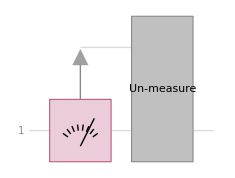

```mathematica
backward["Diagram"]
```

The diagram is two boxes on one wire: the measurement placing its outcome on the pointer record, then the labeled Un-measure block removing it. Apply the whole circuit to the input and read the resulting state:

```mathematica
FullSimplify[ComplexExpand[Normal[backward[psi]["StateVector"]]], {θ ∈ Reals, ϕ ∈ Reals}]
```

{Cos[θ/2],ⅇ^(ⅈ ϕ) Sin[θ/2]}

The state returns as exactly {cos θ/2, e^iϕ sin θ/2}, the input recovered including its phase: the measurement is undone exactly. A projective measurement is irreversible only once its record is discarded; while the record remains a wire, the interaction is reversible, V^†V=I exactly as von Neumann wrote it.

A record, then, is a wire that gates can be conditioned on, that can be traced out, read jointly with the system, or undone. The cost is equally explicit: each measurement appends a pointer qudit, so a circuit with k measurements on n qubits evolves a state of dimension 2^(n+k). That growth is not overhead; it is the cost of retaining every branch, and it is what the teleportation identity, the digitization theorem, and the un-measurement above rely on. Retaining every branch is one computational strategy among several, which leads to the next claim: QF has three.

## Claim 4: One object model, three computational engines

Key feature: the objects of Claims 1 through 3 never specified how they are computed. Underneath a circuit application are three interchangeable engines: exact state-vector algebra (Method -> "Schrodinger"), tensor-network contraction (the default), and a compiled stabilizer tableau (Method -> "Stabilizer"), each suited to a different regime of symbols, structure, and scale. The exact state-vector path is the dense baseline, a literal 2^n matrix-vector product available on demand; the two engines that genuinely change the representation, and so deserve a closer look, are the tensor-network default and the stabilizer tableau, taken in turn. Because all three share one object model, their representations then convert into one another exactly.

Closest competitor. Qiskit Aer exposes the same multi-engine idea through its method= switch across nine backends with automatic selection; what QF adds beyond the switch is that all three representations are one symbolic object that interconverts exactly, plus StabilizerFrame, an exact stabilizer-rank object that falls back automatically at the first non-Clifford gate and carries symbolic parameters through the tableau.

### The default engine: a steered tensor-network contraction

Applying a circuit is, by default, a tensor-network contraction, and the order of the pairwise contractions determines the cost: every step produces an intermediate tensor, the expense is set by the largest intermediate the order creates (in matrix-product language, the bond dimension it requires), and a poor order can be exponentially more expensive than a good one on the same network. QF provides that choice as a Method sub-option, "Path" -> "Greedy" or "Optimal", or an explicit list computed and inspected with GreedyContractionPath / OptimalContractionPath. Take a familiar algorithm: Grover's search for the single input a Boolean oracle accepts among N=2^8=256 candidates. The named "GroverPhase" circuit is one Grover iteration G=D O, the diffusion D after the phase oracle O; stack the peak number of them, k=⌊π/4 √N⌋=12, on the uniform superposition and contract the whole search through a greedily chosen path. The search register size:

```mathematica
n = 8;
```

The marked input, the single accepted candidate among 2^8=256:

```mathematica
marked = 200;
```

Build the Boolean oracle that accepts only that input:

```mathematica
oracle = BooleanFunction[2^marked, n];
```

One Grover iteration G=D O, the diffusion after the phase oracle:

```mathematica
step = QuantumCircuitOperator["GroverPhase"[oracle]]
```

QuantumCircuitOperator[…]

The peak iteration count from the exact rotation angle, k=round(π/(4θ)-1/2) with θ=arcsin √(1/N) (which is 12 here, where the coarser ⌊π/4 √N⌋ agrees):

```mathematica
kopt = Round[Pi/(4 ArcSin[Sqrt[1/2^n]]) - 1/2];
```

The full search: a Hadamard layer, then k stacked iterations:

```mathematica
grover = QuantumCircuitOperator[Join[Thread["H" -> Range[n]], ConstantArray[step, kopt]]]
```

QuantumCircuitOperator[<|Elements -> {QuantumOperator[QuantumState[SparseArray[<4>, {4}], QuantumBasis[<|Input -> QuditBasis[<|{QuditName[0, Dual -> True], 1} -> SparseArray[<1>, {2}], {QuditName[1, Dual -> True], 1} -> SparseArray[<1>, {2}]|>], Output -> QuditBasis[<|{QuditName[0, Dual -> False], 1} -> «1», {«2»} -> «1»|>], «2», ParameterSpec -> {}|>]], {«2»}], «19»}, «1»|>]

Draw the flattened circuit, gate labels off since the diffusion block repeats k times:

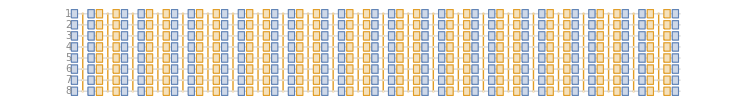

```mathematica
grover["Flatten"]["Diagram", "ShowGateLabels" -> False]
```

Apply it to 0…0 through a greedily chosen contraction path:

```mathematica
found = grover[Method -> {"TensorNetwork", "Path" -> "Greedy"}]
```

QuantumState[…]

Read the largest outcome probability:

```mathematica
Max[found["Probabilities"]]
```

5708688434680186775332495659246923508049077121/5708990770823839524233143877797980545530986496

Because the contraction stayed exact, the probability comes back as an exact rational, a ratio of large integers. Read it as a decimal:

```mathematica
% // N
```

0.999947

The success probability is very close to 1, at the analytic Grover peak sin^2 ((2k+1)arcsin √(1/N)) that the iteration count k=12 is chosen to reach; the most probable bitstring is the marked input itself, 200=11001000 (verified). A search of a few hundred gates, contracted in one steered pass.

The contraction plan is itself an inspectable object. Extract the circuit's tensor network:

```mathematica
net = grover["TensorNetwork"]
```

TensorNetwork[{SparseArray[<1>, {2}], SparseArray[<1>, {2}], SparseArray[<1>, {2}], SparseArray[<1>, {2}], SparseArray[<1>, {2}], SparseArray[<1>, {2}], SparseArray[<1>, {2}], SparseArray[<1>, {2}], SparseArray[<4>, {2, 2}], «410», SparseArray[<4>, {2, 2}], SparseArray[<4>, {2, 2}], SparseArray[<4>, {2, 2}], SparseArray[<4>, {2, 2}], SparseArray[<4>, {2, 2}]}, «1», {«2», «7»}]

Compute the greedy path and draw it as a tree, its branching the order in which the network is folded together:

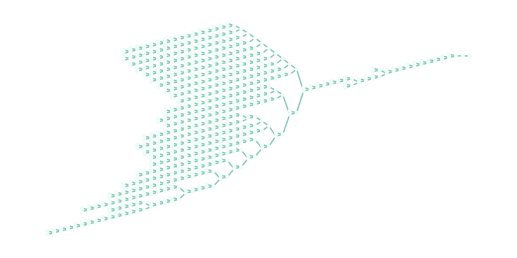

```mathematica
ContractionTree[
 TensorNetworkContraction[net, GreedyContractionPath[net]], 
 TreeElementLabel -> (All -> None), 
 TreeElementShapeFunction -> (All -> None)]
```

The tree is the contraction schedule: the leaves are the circuit's gate and state tensors, every internal node is one pairwise contraction, and the branching structure is the order the greedy path chose, showing which contractions are nested. The depth and balance of that tree are what the path adjusts to keep each intermediate tensor small.

### The stabilizer engine: the state as its symmetry group

For Clifford circuits there is a representation that does not use amplitudes: store the state as the group of Pauli operators that fix it, {P:Pψ=+ψ}, whose n commuting generators determine the n-qubit state uniquely and fit in a binary symplectic tableau. This is the Gottesman-Knill representation, in which a Clifford gate is a constant-size rewrite of the tableau rather than a 2^n×2^n matrix product. The engine is selected by one option. Build a five-qubit linear cluster state, the entangled resource behind measurement-based computing, as a layer of Hadamards followed by nearest-neighbor controlled-Z gates:

```mathematica
cluster5 = QuantumCircuitOperator[
   Join[Thread["H" -> Range[5]],
    {"CZ" -> {1, 2}, "CZ" -> {2, 3}, "CZ" -> {3, 4}, "CZ" -> {4, 5}}]]
```

QuantumCircuitOperator[…]

Draw the circuit:

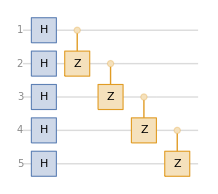

```mathematica
cluster5["Diagram"]
```

The diagram is an ordinary gate-model circuit: a Hadamard on every wire, then controlled-Z gates down the chain 1-2-3-4-5. Nothing about it is stabilizer-specific yet; the engine is a choice made at application time.

Apply it with the stabilizer engine instead of the default:

```mathematica
stab5 = cluster5[Method -> "Stabilizer"]
```

PauliStabilizer[…]

A purely Clifford circuit that would otherwise carry a 2^5 amplitude vector returns instead a PauliStabilizer: the state stored as its symmetry group, not as its amplitudes.

Read the generators of that group:

```mathematica
stab5["PauliForm"]
```

{XZIII,ZXZII,IZXZI,IIZXZ,IIIZX}

Five Pauli strings that determine the state completely. They are exactly the cluster-state generators K_v=X_v∏_(w∼v) Z_w along the chain, the X on each site flanked by Z on its neighbors.

Pauli expectations are closed-form algebra on the generators, with no state vector anywhere:

```mathematica
<|"XZIII" -> stab5["Expectation", "XZIII"], "IZXZI" -> stab5["Expectation", "IZXZI"], "XXIII" -> stab5["Expectation", "XXIII"]|>
```

<|XZIII→1,IZXZI→1,XXIII→0|>

The two generators K_1 and K_3 return deterministically +1, while XX on the first two sites, which anticommutes with K_1=X_1 Z_2, is exactly unbiased, all read off by 𝔽_2 phase tracking.

The advantage of the representation is scale. Apply twenty thousand random Clifford gates to a thousand qubits, a state whose amplitude vector would need 2^1000 entries. The qubit count:

```mathematica
n = 1000;
```

Build the random gate stream, twenty thousand Hadamard, CNOT, and phase gates (seeded for reproducibility):

```mathematica
SeedRandom[1];
gates = Flatten @ Table[{"H" -> RandomInteger[{1, n}], "CNOT" -> RandomSample[Range[n], 2], "S" -> RandomInteger[{1, n}]}, {6666}];
```

Apply them to the n-qubit stabilizer state and time the evolution:

```mathematica
First @ AbsoluteTiming[big = PauliStabilizer[n]["ApplyCircuit", gates];]
```

0.063331

The whole gate stream folds in a fraction of a second: ApplyCircuit runs the tableau updates through one compiled kernel whose per-gate cost is flat in n and independent of the 2^n that never gets built. The cross-engine comparison is boundary-dependent rather than a single ratio: a dedicated C++ tableau (Stim) is roughly 4× faster at the engine core and 11-16× faster end to end, while a Python-driven gate-by-gate pipeline around that same C++ engine is about 27× slower than this one compiled call (measurements in the companion QF-Stabilizer-vs-Packages.md). The bipartite entanglement entropy across the half-chain cut is then a closed form, S(A)=rank_𝔽_2 (generators restricted to A)-A, exact at any qubit count:

```mathematica
big["Entropy", Range[n/2]]
```

496

The entropy returns just below its half-chain maximum: the random circuit has driven the chain to near-maximal, Page-like entanglement, and whatever gate sequence the sampler draws, the value is an exact integer from an 𝔽_2 rank, not an estimate. The boundary of the formalism is handled directly as well: a non-Clifford gate (T, or a general phase) steps outside the stabilizer group, and QF returns a StabilizerFrame, a superposition of stabilizer states, rather than a wrong answer.

### The representations convert exactly

The engines are not separate; one object model means the representations interconvert. Start from an ordinary three-qubit linear cluster circuit, a Hadamard on every wire followed by two nearest-neighbor CZ bonds:

```mathematica
cluster3 = QuantumCircuitOperator[{"H" -> Range[3], "CZ", "CZ" -> {2, 3}}]
```

QuantumCircuitOperator[…]

Draw it:

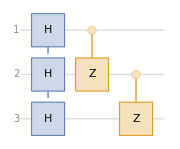

```mathematica
cluster3["Diagram"]
```

The bare "CZ" acts on the default first pair and "CZ" -> {2, 3} on the next, so the diagram shows the bond chain 1-2-3: nothing here is stabilizer-specific, only gates.

Apply that same circuit through the stabilizer engine, which stores the state as its symmetry group rather than its amplitudes:

```mathematica
stab3 = cluster3[Method -> "Stabilizer"]
```

PauliStabilizer[…]

A PauliStabilizer returns, the state held as the three cluster generators that fix it. Now expand that tableau back into an exact state, that is, solve S_i ψ=ψ for the unique joint +1 eigenstate of the three generators:

```mathematica
QuantumState[stab3] // TraditionalForm
```

1/(2 √2)000+1/(2 √2)001+1/(2 √2)010-1/(2 √2)011+1/(2 √2)100+1/(2 √2)101-1/(2 √2)110+1/(2 √2)111

The ket returns as 1/(√8)∑_x (-1)^(x_1 x_2+x_2 x_3)x_1 x_2 x_3: a uniform superposition over all eight bitstrings whose sign is fixed by the two cluster bonds, negative exactly on 011 and 110, the tableau expanded into exact amplitudes. The agreement with the default engine is not approximate; check it with SameQ, the language's structural identity:

```mathematica
QuantumState[stab3]["StateVector"] === cluster3[]["StateVector"]
```

True

True: the two engines produced the same exact expression, global phase included.

The conversion also runs back to circuits: the tableau synthesizes a Clifford circuit that prepares it.

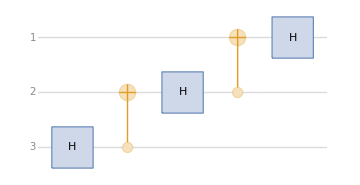

```mathematica
stab3["Circuit"]["Diagram"]
```

A five-gate Clifford circuit returns, interleaved Hadamards and controlled-NOTs, and applying it to 000 reproduces the state vector exactly (verified). Circuit to tableau, tableau to state, tableau back to circuit: three representations of one object, each available where it is cheapest, with symbols, structure, or scale deciding which engine runs.

## Claim 5: A quantum object is an ordinary Wolfram Language expression

Key feature: this is what underlies everything above, the reason Claim 1's algebra is symbolic and Claim 4's three engines share one model: a QF object is a symbolic expression like any other in the language, so the kernel's own functions operate on the object and return another object. Exp exponentiates a generator into a propagator, D differentiates a parametrized gate into another operator, Plus and Commutator build a Hamiltonian from named Paulis, and the closed-form scalars these objects yield pass into solvers like Maximize and Reduce. Nothing is converted, extracted, or exported first: the same Exp, D, Plus one would call on a number-matrix act unchanged on a QuantumOperator and return a QuantumOperator. The overload set is real but finite, Exp (and MatrixExp), D, Plus, Times, Power, Tr, Commutator and the analytic functions act on operators; for Eigenvalues or Det one still reaches through obj["Matrix"].

### Superposition by native arithmetic

Write a state as a sum of kets scaled by amplitudes, and check it against the named one:

```mathematica
(QuantumState["0"] + QuantumState["1"])/Sqrt[2] == QuantumState["+"]
```

True

The comparison returns True: Plus and the scalar division act on the state objects, assembling (0+1)/√2 as a genuine QuantumState, and QF's overloaded == confirms it is +. No amplitudes were extracted by hand, and the same arithmetic extends to the more substantial overloads below.

### The exponential map: a generator becomes a propagator

The propagator of a Hamiltonian H is the matrix exponential e^-iHt. Write it directly, with the kernel's Exp acting on the generator object:

```mathematica
uexp = Exp[(-I t) QuantumOperator["X"]]
```

QuantumOperator[…]

Read its label and its matrix (trig-simplified):

```mathematica
{uexp["Label"], 
 MatrixForm@FullSimplify @ ExpToTrig @ Normal @ uexp["Matrix"]}
```

{ⅇ^(-ⅈ X t),(Cos[t] | -ⅈ Sin[t]
-ⅈ Sin[t] | Cos[t])}

The result is a new QuantumOperator whose label reads e^-iXt and whose matrix is the X-rotation cos t I-isin t X=(cos t | -isin t
-isin t | cos t). Exp performed a genuine matrix exponential on the operator, mixing the two levels through the off-diagonal -isin t rather than exponentiating entries one by one, and the generator was never reduced to a number-matrix first. (MatrixExp[...] returns the identical operator.)

### Operator algebra in one line

Ordinary Plus and scalar multiplication assemble a Hamiltonian on the object, and the Pauli decomposition reads the coefficients back out:

```mathematica
hab = a QuantumOperator["X"] + b QuantumOperator["Z"]
```

QuantumOperator[…]

Read its label and its Pauli decomposition:

```mathematica
{hab["Label"], hab["PauliDecompose"]}
```

{X a+Z b,<|X→a,Z→b|>}

The operator carries the label a X+b Z, and hab["PauliDecompose"] returns <|X -> a, Z -> b|>: a round-trip through the algebra, coefficients in by arithmetic and back out by decomposition, on a symbolic operator rather than a numeric lookup table. The algebra goes beyond arithmetic. The kernel's Commutator gives the su(2) relation as an operator identity:

```mathematica
Commutator[QuantumOperator["X"], QuantumOperator["Y"]] == 2 I QuantumOperator["Z"]
```

True

True: [X,Y]=2iZ, computed on the operators and verified against 2iZ.

### Operator calculus: recover H(t) from a target U(t)

Claim 1 solved Hamiltonians forward into their propagators; the inverse is pure operator calculus. Choose a unitary trajectory U(t), and the Hamiltonian that drives it is H(t)=i U̇(t) U^†(t), the basis of counterdiabatic driving and shortcuts to adiabaticity. Compose the target U(t)=R_Z(t^2) R_X(t) from named gates:

```mathematica
utgt = QuantumOperator["RZ"[t^2]] @ QuantumOperator["RX"[t]]
```

QuantumOperator[…]

Differentiate it as an operator with the kernel's D and close it with the operator's own Dagger, forming H=i U̇ U^†:

```mathematica
hdrive = I D[utgt, t] @ utgt["Dagger"]
```

QuantumOperator[…]

Read the control field off each axis:

```mathematica
FullSimplify[ComplexExpand[#]] & /@ hdrive["PauliDecompose"]
```

<|X→Cos[t^2]/2,Y→Sin[t^2]/2,Z→t,I→0|>

The controls return axis by axis as the drive H(t)=t Z+1/2(cos t^2 X+sin t^2 Y), with a vanishing identity component, traceless as a control should be. D operated on the QuantumOperator and returned a QuantumOperator (not a bare matrix), and composition @, Dagger, and the Pauli decomposition all act on the same object; the defining identity i U̇=H U holds identically. The textbook inverse-design formula runs on the operator itself, with no differential solver involved.

### Calculus on states too

The derivative overload is not operator-only. Take a state whose amplitudes are functions of time. Build it:

```mathematica
psi = QuantumState[{Cos[t], Sin[t]}]
```

QuantumState[…]

Differentiate it twice in place and add it back:

```mathematica
Simplify[D[psi, {t, 2}]["StateVector"] + psi["StateVector"]] // Normal
```

{0,0}

The sum collapses to the zero vector: the object satisfies the harmonic identity ψ''=-ψ through WL's own calculus, the second derivative taken on the QuantumState directly.

### The scalars flow into solvers

When a QF object yields a symbolic scalar, the language's solvers take over. The expectation of X+Z in the trial state R_Y(θ)0 is a closed form. Build the trial state:

```mathematica
psi = QuantumOperator["RY"[θ]][QuantumState["0"]]
```

QuantumState[…]

Form the energy ψ(X+Z)ψ:

```mathematica
energy = Simplify[Conjugate[psi["StateVector"]] . ((QuantumOperator["X"] + QuantumOperator["Z"])[psi])["StateVector"], θ ∈ Reals]
```

Cos[θ]+Sin[θ]

Pass it to Maximize:

```mathematica
Assuming[θ ∈ Reals, Maximize[{energy, 0 <= θ <= 2 Pi}, θ] // FullSimplify]
```

{√2,{θ→π/4}}

The energy is cos θ+sin θ, and Maximize returns √2 at θ=π/4: the exact extremal value, recognizable as the operator norm of X+Z, a complete variational eigenvalue calculation done by composing objects with native arithmetic and optimization. The same approach certifies a physical threshold. The Werner state's realignment criterion, a quantity positive exactly when it witnesses entanglement, is a symbolic function of the mixing p:

```mathematica
crit = Simplify[QuantumEntanglementMonotone[QuantumState["Werner"[p, 2]], "Realignment"], 0 < p < 1]
```

1/2 (-1+Abs[3-4 p])

Turn the criterion into the exact entanglement threshold:

```mathematica
Reduce[crit > 0 && 0 < p < 1, p]
```

0<p<1/2

The criterion is (3-4p-1)/2, and Reduce turns it into the exact threshold: the Werner state is entangled precisely for 0<p<1/2, a physical fact certified by passing a QF-derived expression to a native solver.

## Claim 6: Every object draws itself

Key feature: Claim 5 let the kernel's functions read an object; here the object draws itself. Visualization is property dispatch, not a separate plotting library: each object provides plot properties that render through the Wolfram Language graphics system and forward its options, so a publication figure is one call on the object it depicts. The set of views is wide. States draw as Bloch vectors, amplitude and probability charts, and qudit pie and sector wheels; measurements as outcome histograms; stabilizer states as their binary symplectic tableau; circuits as gate diagrams, tensor-network graphs, and multiway and causal views. Adiabatic evolutions add spectrum, gap, and coupling plots (in the QuantumOptimization sub-package), the underlying TensorNetwork renders as a hypergraph through the TensorNetworks paclet, and the phase-space objects of Claim 2 plot as Wigner surfaces. Below, one example per object kind.

### A state on the Bloch sphere

A single qubit draws its own Bloch vector:

```mathematica
QuantumState[{Cos[Pi/5], Sin[Pi/5] Exp[I Pi/3]}]["BlochPlot"]
```

-Graphics3D-

The output is a Graphics3D of the sphere with the state's arrow at polar angle 2π/5 and azimuth π/3: the geometry of the state, drawn by the state.

### Amplitudes that keep their phases

A bar chart of probabilities discards the phases; AmplitudesChart draws the complex amplitudes ψ_x=xψ themselves, heights for the magnitudes ψ_x and colors for the phases arg ψ_x. Apply a quantum Fourier transform to the two-term superposition 1/(√2)(000+101), which the transform spreads into a phase-rich pattern across all eight basis states:

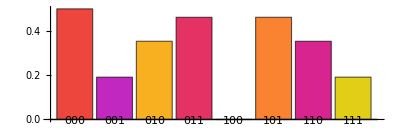

```mathematica
QuantumCircuitOperator["Fourier"[3]][
  QuantumState[Normalize[{1, 0, 0, 0, 0, 1, 0, 0}]]]["AmplitudesChart", 
 ChartLegends -> Automatic, AspectRatio -> 1/3, 
 PlotRange -> {Automatic, 1}]
```

The eight bars return with magnitudes tracing an interference comb, a clean null at 100, and the surviving bars tinted by a wheel of distinct phase colors keyed by the legend: the QFT's phase ramp made visible alongside the magnitudes, the full complex state in one figure.

### A measurement draws its statistics

A QuantumMeasurement object charts its own outcome distribution, the Born probabilities p(x)=xψ^2. Run the Bernstein-Vazirani circuit for a hidden string s=1011, a single oracle query that encodes s in the interference pattern, and let it draw the statistics of its own final measurement:

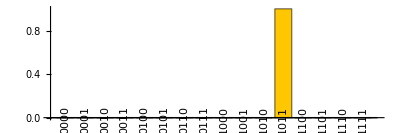

```mathematica
QuantumCircuitOperator[
   "BernsteinVazirani"[{1, 0, 1, 1}]][]["ProbabilitiesPlot", 
 "LabelsAngle" -> 90 Degree, AspectRatio -> 1/3]
```

The histogram collapses to a single bar of height 1 at 1011, every other outcome exactly zero: one query has extracted the entire hidden string from the Born statistics, the deterministic signature of the algorithm. The hardware result in Claim 7 is the same kind of object, which is why simulated and measured statistics compare so directly there.

### A stabilizer state shows its tableau

The stabilizer states of Claim 4 have a native picture of their own: the binary symplectic tableau, the actual data structure the formalism computes on. Feed the five-cycle graph C_5 straight into PauliStabilizer to build its ring cluster state, and draw the tableau:

```mathematica
PauliStabilizer[QuantumCircuitOperator["Graph"[CycleGraph[5]]]]["TableauForm"]
```

(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0)

The display is the sign column beside a ten-by-ten binary grid, dividers separating the x bits from the z bits and the destabilizer rows from the stabilizer rows; the stabilizer rows are the five ring generators K_v=X_v∏_(w∼v) Z_w, so the z block is literally the adjacency matrix of the cycle while the x block is the identity. This view is the algebra itself: the entanglement geometry of the ring is drawn in the binary pattern, and a Clifford gate acts by rewriting a few columns of this grid.

### The circuit, and the network behind it

A circuit draws itself as a gate diagram. Take quantum phase estimation, the subroutine inside Shor's factoring and the HHL linear solver, on three counting qubits:

```mathematica
qpe = QuantumCircuitOperator["PhaseEstimation"[3]]
```

QuantumCircuitOperator[…]

Draw it as a gate diagram:

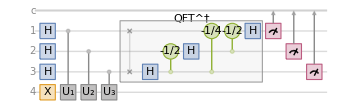

```mathematica
qpe["Diagram"]
```

The wire-and-gate picture lays out the algorithm: Hadamards on the counting register, the controlled powers of the unitary, and the inverse Fourier transform that reads the phase back. The same object also draws its internal structure, the tensor network that the engine contracts:

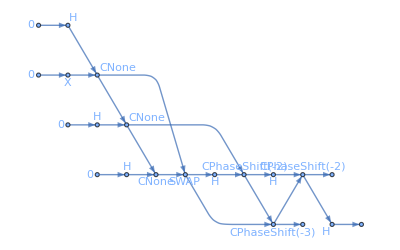

```mathematica
qpe["TensorNetworkGraph"]
```

A Graph whose vertices are the gate and state tensors and whose edges are the contracted indices: the diagram shows the physics, the network shows the computation, and Claim 4 steered the order in which such a network is contracted.

The same network renders in the dual picture too, as a hypergraph in which the roles swap, every index a vertex and every tensor one hyperedge spanning its indices:

```mathematica
qpe["TensorNetwork"]["Hypergraph"]
```

-Graphics-

The result is a Hypergraph with one hyperedge per tensor of the phase-estimation circuit, drawn over the network's indices: the tensor-contraction picture of the algorithm, in which contracting two tensors is the merging of two hyperedges.

## Claim 7: An interoperability hub, down to real hardware

Key feature: the objects so far stayed inside QF; this claim sends them out. A QF object can leave QF for the rest of the quantum ecosystem, and foreign circuits can enter it; QuantumQASM is the single OpenQASM interface, and it runs in pure Wolfram Language with no external account. Each step below extends the interface: text export, foreign import, device-aware transpilation, and finally a physical quantum processor.

Closest competitor. Posting OpenQASM to a hardware provider is not itself unusual, MATLAB has submitted circuits to IBM Python-free since R2023b; the defensible part here is that device-native ISA transpilation runs in Wolfram Language and the same symbolic objects leave and re-enter the framework unchanged.

### Export to OpenQASM 3.0 (native, no Python)

QuantumQASM turns a circuit into the standard text format read by Qiskit, Cirq, and most hardware stacks.

```mathematica
QuantumQASM[QuantumCircuitOperator["Toffoli"]]
```

OPENQASM 3.0;
qubit[3] q;
bit[0] c;
U(1.5707963267948966, 0., 3.141592653589793) q[2];
ctrl(1) @ negctrl(0) @ U(3.141592653589793, 0., 3.141592653589793) q[1] q[2];
U(0., 0., 5.497787143782138) q[2];
ctrl(1) @ negctrl(0) @ U(3.141592653589793, 0., 3.141592653589793) q[0] q[2];
U(0., 0., 0.7853981633974483) q[2];
ctrl(1) @ negctrl(0) @ U(3.141592653589793, 0., 3.141592653589793) q[1] q[2];
U(0., 0., 5.497787143782138) q[2];
ctrl(1) @ negctrl(0) @ U(3.141592653589793, 0., 3.141592653589793) q[0] q[2];
U(0., 0., 0.7853981633974483) q[1];
U(0., 0., 0.7853981633974483) q[2];
U(1.5707963267948966, 0., 3.141592653589793) q[2];
ctrl(1) @ negctrl(0) @ U(3.141592653589793, 0., 3.141592653589793) q[0] q[1];
U(0., 0., 0.7853981633974483) q[0];
U(0., 0., 5.497787143782138) q[1];
ctrl(1) @ negctrl(0) @ U(3.141592653589793, 0., 3.141592653589793) q[0] q[1];

The output is a complete OpenQASM 3.0 program for the three-qubit Toffoli gate: rather than a single ccx instruction, the emitter writes the standard Clifford+T decomposition, six CNOTs (each a ctrl @ U) interleaved with the non-Clifford T and T^† phases and a pair of Hadamards bracketing the target, every gate a concrete U rotation. The native emitter writes OpenQASM 3.0, and the importer below reads OpenQASM 2.0 or 3.0 alike. A 2.0 export is available through the qiskit path, QuantumQASM[circuit, "Version" -> 2] (that route needs Python; the 3.0 export and all imports do not). Export needs concrete angles: a circuit with a symbolic parameter returns a Failure rather than a QASM string, so resolve parameters to numbers at this boundary while keeping them symbolic everywhere else in QF (Claims 1 and 5).

### Import foreign OpenQASM and compute with it (native, no Python)

The same interface runs the other way: give QuantumCircuitOperator an OpenQASM string authored anywhere and get back a QF circuit, parsed in pure WL, including reset, controlled gates, and mid-circuit measure. The importer reads each gate's angle as a Wolfram Language expression, so the angles can stay symbolic: write Pi/2 and Pi, the exact constant, in place of their decimal expansions, and the imported circuit is exact rather than a floating-point copy. Import a four-qubit circuit that runs the optimal quantum strategy for the CHSH game:

```mathematica
chsh = QuantumCircuitOperator["OPENQASM 3.0;
qubit[4] q;
bit[4] c;
reset q[0];
reset q[3];
U(Pi/2, 0, Pi) q[3];
U(Pi/2, 0, Pi) q[0];
swap q[0] q[3];
ctrl(0) @ negctrl(1) @ U(Pi/2, Pi, Pi) q[0] q[3];
ctrl(1) @ negctrl(0) @ U(Pi/2, 0, 0) q[0] q[3];
reset q[1];
U(Pi/2, 0, Pi) q[1];
reset q[2];
U(Pi/2, 0, Pi) q[2];
U(0, 0, 0) q[0];
ctrl(1) @ negctrl(0) @ U(Pi/2, 0, Pi) q[1] q[0];
U(Pi/4, 0, 0) q[3];
ctrl(0) @ negctrl(1) @ U(Pi/2, 0, Pi) q[2] q[3];
c[0] = measure q[0];
c[1] = measure q[1];
c[2] = measure q[2];
c[3] = measure q[3];"]
```

QuantumCircuitOperator[…]

Note that QF reads U(Pi/2, 0, Pi): the angle is the Wolfram constant Pi. A spec-strict OpenQASM 3 parser like qiskit knows only the lowercase pi and rejects Pi as an undefined symbol.

Once imported it is an ordinary QF object, exact end to end because every angle stayed a symbol.

In the CHSH game the players win when their answers satisfy x⋀y=a⊕b, and no classical strategy wins more than 3/4 of the time; entanglement beats that bound. Read the circuit's joint measurement distribution, label the four outcomes (a,x,y,b), and ask Wolfram Language for the winning probability Pr, in closed form:

```mathematica
Probability[BitAnd[x, y] == BitXor[a, b], {a, x, y, b} \[Distributed] chsh[]["MultivariateDistribution"]] // FullSimplify
```

1/4 (2+√2)

Because the angles never left exact arithmetic, the winning probability returns as a closed form, (2+√2)/4=cos^2 (π/8), exactly the Tsirelson bound, the quantum maximum for CHSH and the algebraic number a sampled estimate only converges toward. A circuit authored in another tool became an exact probability read off with native WL statistics.

### A hardware-aware transpilation target

QiskitTarget carries a device spec (qubit count, native gate set, connectivity), validated at construction against qiskit's own Target schema through the Python bridge. Build a 5-qubit linear-chain device:

```mathematica
target = QiskitTarget[<|"NumQubits" -> 5, "BasisGates" -> {"cx", "rz", "sx", "x"},
   "CouplingMap" -> {{0,1},{1,2},{2,3},{3,4}}|>]
```

QiskitTarget[…]

Read its coupling map back:

```mathematica
target["CouplingMap"]
```

{{0,1},{1,2},{2,3},{3,4}}

Pass the target to QuantumQASM as an option, and the circuit is transpiled to that backend's native gates and connectivity:

```mathematica
QuantumQASM[QuantumCircuitOperator["Fourier"[3]], "Target" -> target]
```

OPENQASM 3.0;
include "stdgates.inc";
rz(7*pi/8) $0;
rz(-pi/2) $1;
sx $1;
rz(-2.677945044588988) $1;
rz(-pi/2) $2;
cx $1, $2;
x $1;
rz(pi/4) $2;
cx $1, $2;
rz(2.819842099193151) $1;
cx $0, $1;
rz(-pi/8) $1;
cx $0, $1;
rz(5*pi/8) $1;
rz(-pi/4) $2;
sx $2;
rz(-pi/2) $2;
cx $1, $2;
sx $1;
rz(pi) $1;
rz(pi/2) $2;
sx $2;
rz(pi/2) $2;
cx $1, $2;
sx $1;
rz(pi/2) $1;
rz(pi/2) $2;
sx $2;
rz(pi/2) $2;
cx $1, $2;
cx $0, $1;
rz(-pi/4) $1;
cx $0, $1;
sx $0;
rz(pi/2) $0;
rz(pi/4) $1;

The QFT comes back rewritten for the device: its controlled-phase rotations decomposed into the native rz/sx/x set, the entangling steps as cx on physical qubits, every two-qubit gate routed along an edge the coupling map allows. Transpiling a Fourier transform, with its all-to-all controlled phases, is a realistic instance of this task, where both decomposition and routing are non-trivial.

### Submit to a real IBM QPU, and compare to the exact result

An IBM account connects through ServiceConnect["IBMQuantumPlatform"], after which IBMJobSubmit sends a circuit to the hardware asynchronously and returns an IBMJob handle. Create an API key and copy your instance's cloud resource name (CRN) from your IBM Quantum Platform account, then connect, the placeholder "xxx" values standing in for your own:

```mathematica
api = "XXX";
LocalSymbol["ibm_crn"] = "XXX";
ServiceConnect["IBMQuantumPlatform", "New", Authentication -> {"apikey" -> api}]
```

ServiceObject[…]

The call returns a ServiceObject connection handle. A QPU job needs a circuit that ends in a measurement; in QF a list of qubit indices placed in the circuit is exactly that, so {1, 2, 3} measures all three qubits. Build the measured GHZ circuit:

```mathematica
ghz = QuantumCircuitOperator[{"GHZ"[3], {1, 2, 3}}]
```

QuantumCircuitOperator[…]

Submit it to the backend, which returns a handle immediately:

```mathematica
job = IBMJobSubmit[ghz, "ibm_fez", "Shots" -> 4096]
```

IBMJob[…]

Check the status:

```mathematica
job["Status"]
```

Queued

The handle returns immediately with status "Queued" while the job waits in the device queue. The same circuit runs exactly in the Wolfram Language by applying it:

```mathematica
wl = ghz[]
```

QuantumMeasurement[…]

The result is a QuantumMeasurement with probabilities 1/2 at 000 and 1/2 at 111. Once the job completes, the hardware outcome comes back as the same kind of QuantumMeasurement object, decoded into the same qubit order:

```mathematica
qpu = job["Refresh"][]
```

QuantumMeasurement[…]

This run returned 4096 shots from ibm_fez. Because the two results are the same kind of object, hardware noise can be shown in one chart, the exact and measured probabilities paired per basis state:

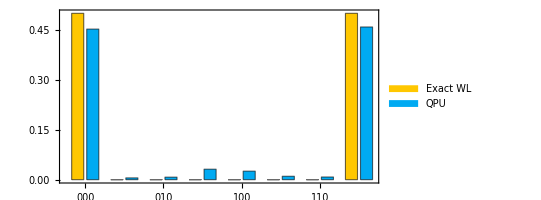

```mathematica
BarChart[Transpose[Values @* KeySort /@ {wl["Probabilities"], qpu["Probabilities"]}],
  AspectRatio -> 1/2, Frame -> True, ChartLegends -> {"Exact WL", "QPU"},
  PlotLabels -> Keys[wl["Probabilities"]]]
```

The exact bars are 1/2 at 000 and 111 and zero elsewhere; the device's two tall bars fall visibly short of 1/2, with the missing weight spread thinly over the six bitstrings the exact state forbids. That gap, read bar by bar from one figure, is the device noise.

## Where This Stops

Every closed form in this document rests on one fact, and so does its limit: a symbolic result exists exactly as far as the underlying spectrum is solvable in radicals. The eigenvalues of a matrix up to 4×4 are closed-form (radicals reach through the quartic); at 5×5 and beyond they are generically Root objects with no elementary form, by Abel-Ruffini. That algebraic boundary, not the qubit count, is where the symbolic path ends.

Two of the results above sit at this boundary. The many-body entanglement entropy of Claim 1 is -Tr[ρ_1 log_2 ρ_1], a function of the eigenvalues of the reduced density matrix; it stays a formula while ρ_1 is at most 4×4, and once a larger block is traced out those eigenvalues become quintic roots and the entropy loses its closed form. The master equation of Claim 2 solves symbolically only when the Liouvillian's spectrum is solvable: the structured relaxation there returns a closed form at once, but a generically driven open system, whose secular determinant is a high-degree or unstructured polynomial, returns an unwieldy radical expression or nothing in workable time.

So the scope is narrow and exact. QF carries a computation to closed form precisely when the physics has a closed-form spectrum, and it indicates the limit by returning a Root object the moment that fails, rather than a wrong answer or a silent truncation. The symbolic path is deep, not wide: it runs as far as the algebra allows and stops at the boundary set by Abel and Ruffini. Beyond that boundary the same objects still compute, now numerically, which is why every claim above also has a purely numeric reading.

## Where This Leaves Us

Seven claims, each demonstrated in executed code. Symbolic algebra carried dynamics to closed form: the Rabi propagator of a rotating drive, a Landau-Zener sweep expressed in parabolic cylinder functions, a QAOA landscape whose exact maximum is a closed-form cubic root, the entanglement entropy of a quench as a function of time. One object model held the rest of the theory: channels, POVMs, Fock space, and phase space; a master equation solved once for every initial state and every rate, with T_2≤2 T_1 arriving as a theorem rather than a remembered rule; a basis and a dimension on every object, a spin-1 Hamiltonian and a five-site ring each diagonalized by its own named basis; a state reconstructed from measured counts at a fidelity close to 1. Measurement stayed inside the physics: records became quantum wires, teleportation carried its classical channel as a quantum wire, a coherent error was digitized and corrected at codeword fidelity exactly 1, and a measurement ran backwards. Underneath, three engines computed the same objects: exact state-vector algebra, a steered tensor-network contraction, and a stabilizer tableau that carried a thousand qubits to near-maximal half-chain entanglement computed exactly, the representations converting into one another exactly. Because these objects are ordinary Wolfram Language expressions, the kernel's own functions transformed them directly, exponentiating a generator into its propagator and differentiating a gate to recover the Hamiltonian that drives it, and each of them drew itself. And the same objects left the system: out to OpenQASM and back, through a transpiler to a device's native gates, and onto a physical quantum processor, whose 4096-shot histogram stands in this document next to the exact distribution it approximates.

Behind all seven claims is one mechanism: quantum objects that are exact symbolic expressions compose, with each other and with the entire language. One consequence ran through every example: the result was exact, the algebraic QAOA optimum, the closed-form relaxation law, the integer stabilizer entropy, the exactly-recovered teleported state, never a value sampled near the answer but the exact quantity such a sample converges toward. That is the numerical claim underlying the symbolic one: where a numeric simulation or a finite measurement returns an estimate, QF returns the exact object it estimates. The distance from writing a Hamiltonian to reading its closed form, or to running it on hardware, is a few composable calls. A result that is a formula can be differentiated, reduced, or taken to a limit; a result that is a circuit is already in the format the rest of the quantum ecosystem uses.

The next steps are the reader's: change the graph under the QAOA section, raise the spin past 1, swap damping for dephasing, tilt the repetition code's coherent error off the X axis, point the last section at a different backend. The document re-derives itself.

Setup. Evaluate once before the cells; this installs the development builds of the QuantumFramework and TensorNetworks paclets and loads them:

```mathematica
PacletInstall["https://www.wolfr.am/DevWQCF", 
 ForceVersionInstall -> True];
Needs["Wolfram`QuantumFramework`"]
Needs["Wolfram`QuantumFramework`SecondQuantization`"];
PacletInstall["https://www.wolfr.am/DevWTN", 
 ForceVersionInstall -> True];
Needs["Wolfram`TensorNetworks`"];
```

QuantumBasis::shdw: Symbol QuantumBasis appears in multiple contexts {Wolfram`QuantumFramework`,Global`}; definitions in context Wolfram`QuantumFramework` may shadow or be shadowed by other definitions.

QuantumChannel::shdw: Symbol QuantumChannel appears in multiple contexts {Wolfram`QuantumFramework`,Global`}; definitions in context Wolfram`QuantumFramework` may shadow or be shadowed by other definitions.

IBMJobSubmit::shdw: Symbol IBMJobSubmit appears in multiple contexts {Wolfram`QuantumFramework`,Global`}; definitions in context Wolfram`QuantumFramework` may shadow or be shadowed by other definitions.

QuantumCircuitOperator::shdw: Symbol QuantumCircuitOperator appears in multiple contexts {Wolfram`QuantumFramework`,Global`}; definitions in context Wolfram`QuantumFramework` may shadow or be shadowed by other definitions.

QuantumQASM::shdw: Symbol QuantumQASM appears in multiple contexts {Wolfram`QuantumFramework`,Global`}; definitions in context Wolfram`QuantumFramework` may shadow or be shadowed by other definitions.

QiskitTarget::shdw: Symbol QiskitTarget appears in multiple contexts {Wolfram`QuantumFramework`,Global`}; definitions in context Wolfram`QuantumFramework` may shadow or be shadowed by other definitions.

QuantumSimilarity::shdw: Symbol QuantumSimilarity appears in multiple contexts {Wolfram`QuantumFramework`,Global`}; definitions in context Wolfram`QuantumFramework` may shadow or be shadowed by other definitions.

QuantumEntanglementMonotone::shdw: Symbol QuantumEntanglementMonotone appears in multiple contexts {Wolfram`QuantumFramework`,Global`}; definitions in context Wolfram`QuantumFramework` may shadow or be shadowed by other definitions.

QuantumEvolve::shdw: Symbol QuantumEvolve appears in multiple contexts {Wolfram`QuantumFramework`,Global`}; definitions in context Wolfram`QuantumFramework` may shadow or be shadowed by other definitions.

QuantumMeasurementOperator::shdw: Symbol QuantumMeasurementOperator appears in multiple contexts {Wolfram`QuantumFramework`,Global`}; definitions in context Wolfram`QuantumFramework` may shadow or be shadowed by other definitions.

QuantumOperator::shdw: Symbol QuantumOperator appears in multiple contexts {Wolfram`QuantumFramework`,Global`}; definitions in context Wolfram`QuantumFramework` may shadow or be shadowed by other definitions.

QuantumPartialTrace::shdw: Symbol QuantumPartialTrace appears in multiple contexts {Wolfram`QuantumFramework`,Global`}; definitions in context Wolfram`QuantumFramework` may shadow or be shadowed by other definitions.

QuantumMeasurementSimulation::shdw: Symbol QuantumMeasurementSimulation appears in multiple contexts {Wolfram`QuantumFramework`,Global`}; definitions in context Wolfram`QuantumFramework` may shadow or be shadowed by other definitions.

QuantumStateEstimate::shdw: Symbol QuantumStateEstimate appears in multiple contexts {Wolfram`QuantumFramework`,Global`}; definitions in context Wolfram`QuantumFramework` may shadow or be shadowed by other definitions.

QuantumState::shdw: Symbol QuantumState appears in multiple contexts {Wolfram`QuantumFramework`,Global`}; definitions in context Wolfram`QuantumFramework` may shadow or be shadowed by other definitions.

QuantumTensorProduct::shdw: Symbol QuantumTensorProduct appears in multiple contexts {Wolfram`QuantumFramework`,Global`}; definitions in context Wolfram`QuantumFramework` may shadow or be shadowed by other definitions.

PauliStabilizer::shdw: Symbol PauliStabilizer appears in multiple contexts {Wolfram`QuantumFramework`,Global`}; definitions in context Wolfram`QuantumFramework` may shadow or be shadowed by other definitions.

GreedyContractionPath::shdw: Symbol GreedyContractionPath appears in multiple contexts {Wolfram`TensorNetworks`,Global`}; definitions in context Wolfram`TensorNetworks` may shadow or be shadowed by other definitions.

TensorNetworkContraction::shdw: Symbol TensorNetworkContraction appears in multiple contexts {Wolfram`TensorNetworks`,Global`}; definitions in context Wolfram`TensorNetworks` may shadow or be shadowed by other definitions.

ContractionTree::shdw: Symbol ContractionTree appears in multiple contexts {Wolfram`TensorNetworks`,Global`}; definitions in context Wolfram`TensorNetworks` may shadow or be shadowed by other definitions.

AnnihilationOperator::shdw: Symbol AnnihilationOperator appears in multiple contexts {Wolfram`QuantumFramework`SecondQuantization`,Global`}; definitions in context Wolfram`QuantumFramework`SecondQuantization` may shadow or be shadowed by other definitions.

WignerRepresentation::shdw: Symbol WignerRepresentation appears in multiple contexts {Wolfram`QuantumFramework`SecondQuantization`,Global`}; definitions in context Wolfram`QuantumFramework`SecondQuantization` may shadow or be shadowed by other definitions.

HusimiQRepresentation::shdw: Symbol HusimiQRepresentation appears in multiple contexts {Wolfram`QuantumFramework`SecondQuantization`,Global`}; definitions in context Wolfram`QuantumFramework`SecondQuantization` may shadow or be shadowed by other definitions.

CoherentState::shdw: Symbol CoherentState appears in multiple contexts {Wolfram`QuantumFramework`SecondQuantization`,Global`}; definitions in context Wolfram`QuantumFramework`SecondQuantization` may shadow or be shadowed by other definitions.

FockState::shdw: Symbol FockState appears in multiple contexts {Wolfram`QuantumFramework`SecondQuantization`,Global`}; definitions in context Wolfram`QuantumFramework`SecondQuantization` may shadow or be shadowed by other definitions.

ThermalState::shdw: Symbol ThermalState appears in multiple contexts {Wolfram`QuantumFramework`SecondQuantization`,Global`}; definitions in context Wolfram`QuantumFramework`SecondQuantization` may shadow or be shadowed by other definitions.

CatState::shdw: Symbol CatState appears in multiple contexts {Wolfram`QuantumFramework`SecondQuantization`,Global`}; definitions in context Wolfram`QuantumFramework`SecondQuantization` may shadow or be shadowed by other definitions.

G2Coherence::shdw: Symbol G2Coherence appears in multiple contexts {Wolfram`QuantumFramework`SecondQuantization`,Global`}; definitions in context Wolfram`QuantumFramework`SecondQuantization` may shadow or be shadowed by other definitions.

Every cell was executed as shown (Wolfram Language 15.0, Wolfram/QuantumFramework 2.0.0) and every stated output is the captured result, including the hardware run on ibm_fez; reproducing the transpilation cells needs a Python installation with qiskit, and the hardware cells an IBM Quantum account.

Taken together, these features, and above all the way symbolic algebra, numerical simulation, and visualization live inside one object, make QF a particularly effective tool for teaching and learning quantum theory at every level, from a first qubit to graduate research: a student can build a state, evolve it, draw it, and read its closed form in a single expression, the computation-first habit this document follows throughout. Wolfram develops that direction directly, in the book Quantum Computing by Model and Simulation: A Computational Approach (Wolfram Media), which teaches the subject through modeling and simulation in the framework, and in Wolfram U, whose free interactive courses and study groups include quantum computing and related topics.